## Preamble

```mathematica
SetDirectory[NotebookDirectory[]];
FMdir="FMs//";
```

### Fiducial Model & Miscellanea

```mathematica
hh=0.7;Ωm0fid=0.3;σintfid =0.13;σ8fid=.83;γfid=0.545;
kmin=0.005;
kmax=0.1;
(* kmax3 = 0.3; *)
fskyLSST=18000/(180/π)^2 1./(4π);
const=(Log[10]/5.)^2 2998^2/10^6;
σvnonlinoverH0sq=(300./299800)^2*2998^2; (* σv^2 / H0^2 *)
```

```mathematica
colordd=RGBColor[{65,144,210}/255];
color1a=Darker[colordd,.15];
color2=RGBColor[{138,32,13}/255];
colordv=Orange;
colorvvold=RGBColor[{65,144,10}/255];
colorvv=Lighter[colorvvold,.6];
colorvva=RGBColor[{11,184,1}/256*.85];
colorfull=RGBColor[{159,19,107}/256*1.2];
color6x2=colordv;
{colordd,color2,colorvv,colorfull}
```

{RGBColor[{Rational[13, 51], Rational[48, 85], Rational[14, 17]}],RGBColor[{Rational[46, 85], Rational[32, 255], Rational[13, 255]}],RGBColor[0.7019607843137254, 0.8258823529411765, 0.6156862745098038],RGBColor[{0.7453124999999999, 0.0890625, 0.5015625}]}

```mathematica
FMpranges8LSST={{6 10^-6,7 10^-4},{0.05,6}};
FMprangeγLSST={{6 10^-6,7 10^-4},{0.05,6}};
```

```mathematica
σ8list=Range[0,2,.02];
γlist=Range[-1,2.5,.038];
σ8listzoom=Range[.5,1.2,.007];
γlistzoom=Range[-.2,1.4,.018];
blist=Range[.4,2.6,.022];
{Dimensions[σ8list],Dimensions[γlist],Dimensions[blist],Dimensions[σ8listzoom],Dimensions[γlistzoom]}
```

{{101},{93},{101},{101},{89}}

### Contour Function

```mathematica
Clear[contourfun]
contourfun[chisq_]:=Module[{dchiqAux,lhoodAuxInt},
dchiqAux=chisq[[All,All,3]]-Min[chisq[[All,All,3]]];  (*chiq2D is the 2D marginalized χ^2*)
lhoodAuxInt=Total[Exp[-(dchiqAux/2)],2];
f[z_]:=Catch[Do[
{sigma1=0,
Do[If[dchiqAux[[i,j]]<z,sigma1+=Exp[-dchiqAux[[i,j]]/2]],{i,1,Dimensions[dchiqAux][[1]]},{j,1,Dimensions[dchiqAux][[2]]}],Throw[sigma1/lhoodAuxInt]}
,{1}]];
g=Interpolation[Partition[Riffle[Range[0,16.5,.3],Map[f,Range[0,16.5,.3]]],2],InterpolationOrder->2];
c1sig=z/.Minimize[{(g[z]-.6827)^2,.1<z<7},z][[2]];
c2sig=z/.Minimize[{(g[z]-.9545)^2,1<z<11},z][[2]];
c3sig=z/.Minimize[{(g[z]-.9973)^2,3<z<16},z][[2]];
contours={c1sig,c2sig,c3sig};
Print[Map[g,contours]];
contours
]
```

```mathematica
(* assumes FM has zbins as last dimension *)
FMchisqfunold[zbinmin_,zbinmax_]:=Module[{FMtemp,FMtempchisq},
Dimensions[FMtemp=Total[FMbins[[All,All,zbinmin;;zbinmax]],{3}]];
FMtempchisq=Table[{s8,γ,{s8-.83,γ-.55}.FMtemp.{s8-.83,γ-.55}},{s8,σ8list},{γ,γlist}];
Flatten[FMtempchisq,1]
]
```

```mathematica
(* assumes FM has zbins as first dimension *)
Clear[FMfixchisqfun,FMmargchisqfun]
FMfixchisqfun[FMbins_,zbinmin_,zbinmax_,ip1_,p1fid_,p1list_,ip2_,p2fid_,p2list_]:=Module[{FMtemp,FMtempchisq},
FMtemp=Total[FMbins[[zbinmin;;zbinmax,{ip1,ip2},{ip1,ip2}]],{1}]+FMprior[[{ip1,ip2},{ip1,ip2}]];
FMtempchisq=Table[{p1,p2,{p1-p1fid,p2-p2fid}.FMtemp.{p1-p1fid,p2-p2fid}},{p1,p1list},{p2,p2list}];
flat=Flatten[FMtempchisq,1];
flat[[All,3]]-=Min[flat[[All,3]]];
flat
]
FMmargchisqfun[FMbins_,zbinmin_,zbinmax_,ip1_,p1fid_,p1list_,ip2_,p2fid_,p2list_]:=Module[{FMtemp,FMmarg,FMtempchisq,cov},
FMtemp=Total[FMbins[[zbinmin;;zbinmax,All,All]],{1}]+FMprior;
cov=Inverse[FMtemp];
FMmarg=Inverse[cov[[{ip1,ip2},{ip1,ip2}]]];
FMtempchisq=Table[{p1,p2,{p1-p1fid,p2-p2fid}.FMmarg.{p1-p1fid,p2-p2fid}},{p1,p1list},{p2,p2list}];
flat=Flatten[FMtempchisq,1];
flat[[All,3]]-=Min[flat[[All,3]]];
flat
]
FMfixσchisqfun[FMbins_,zbinmin_,zbinmax_,ip1_,p1fid_,p1list_,ip2_,p2fid_,p2list_]:=Module[{FMtemp,FMmarg,FMtempchisq,cov},
FMtemp=Total[FMbins[[zbinmin;;zbinmax,;;-3,;;-3]],{1}]+FMprior[[;;-3,;;-3]];
cov=Inverse[FMtemp];
FMmarg=Inverse[cov[[{ip1,ip2},{ip1,ip2}]]];
FMtempchisq=Table[{p1,p2,{p1-p1fid,p2-p2fid}.FMmarg.{p1-p1fid,p2-p2fid}},{p1,p1list},{p2,p2list}];
flat=Flatten[FMtempchisq,1];
flat[[All,3]]-=Min[flat[[All,3]]];
flat
]

FMCMBchisqfun[FMbins_,p1fid_,p1list_,p2fid_,p2list_]:=Module[{FMtemp,FMmarg,FMtempchisq,cov},
FMtemp=FMbins[[All,All]];
FMtempchisq=Table[{p1,p2,{p1-p1fid,p2-p2fid}.FMtemp.{p1-p1fid,p2-p2fid}},{p1,p1list},{p2,p2list}];
flat=Flatten[FMtempchisq,1];
flat[[All,3]]-=Min[flat[[All,3]]];
flat
]
```

```mathematica
fstyle=17+3;
lplotddfun[chisq_,cont123_,labels_]:=ListContourPlot[chisq,Contours->cont123,ContourStyle->Directive[{Darker[colordd,.4],Thickness[.007],Opacity[.9]}],ContourShading->{Darker[colordd,.1],Lighter[colordd,.1],Lighter[colordd,.5],Transparent},FrameLabel->labels,FrameStyle->fstyle];
lplotdvfun[chisq_,cont123_,labels_]:=ListContourPlot[chisq,Contours->cont123,ContourStyle->Directive[{Darker[colordv,.5],Thickness[.007],Opacity[.9]}],ContourShading->{Darker[colordv,.2],colordv,Lighter[colordv],Transparent},FrameLabel->labels,FrameStyle->fstyle];
lplotvvfun[chisq_,cont123_,labels_]:=ListContourPlot[chisq,Contours->cont123,ContourStyle->Directive[{Darker[colorvv,.5],Thickness[.007],Opacity[.9]}],ContourShading->{Darker[colorvv,.2],colorvv,Lighter[colorvv],Transparent},FrameLabel->labels,FrameStyle->fstyle];
lplotfullfun[chisq_,cont123_,labels_]:=ListContourPlot[chisq,Contours->cont123,ContourStyle->Directive[{Darker[colorfull,.4],Thickness[.007],Opacity[.9]}],ContourShading->{Darker[colorfull,.1],Lighter[colorfull,.1],Lighter[colorfull,.5],Transparent},FrameLabel->labels,FrameStyle->fstyle];
lplot6x2fun[chisq_,cont123_,labels_]:=ListContourPlot[chisq,Contours->cont123,ContourStyle->Directive[{Darker[colorfull,.4],Thickness[.007],Opacity[.9]}],ContourShading->{Darker[color6x2,.1],Lighter[color6x2,.1],Lighter[color6x2,.5],Transparent},FrameLabel->labels,FrameStyle->fstyle];
lplotpriorfun[chisq_,cont123_,labels_]:=ListContourPlot[chisq,Contours->cont123,ContourStyle->Directive[{Black,Dashed,Thickness[.007],Opacity[.8]}],ContourShading->{Transparent,Transparent,Transparent,Transparent},FrameLabel->labels,FrameStyle->fstyle];
lplotcmbfun[chisq_,cont123_,labels_]:=ListContourPlot[chisq,Contours->cont123,ContourStyle->Directive[{Darker[colorvvold,.3],Thickness[.005],Opacity[.8]}],ContourShading->{Darker[colorvvold,.25],Lighter[colorvvold,.05],Transparent},FrameLabel->labels,FrameStyle->fstyle];
```

### Importing CAMB spectra

```mathematica
cambdir="camb\\";
```

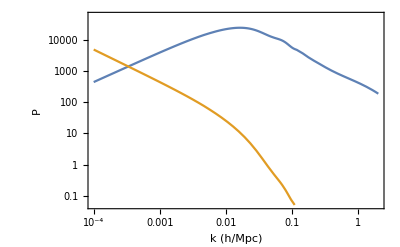

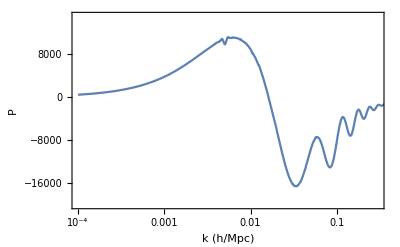

```mathematica
σ8camb=0.83;

power=Import[cambdir<>"camb_64063872_matterpower_z0.dat","Table"];
powerinterp=Interpolation[power];
dPmmdlnk[k_]=(x D[powerinterp[x], x])/.x->k;
powervv=power; (* radial velocity Power Spectrum *)
powervv[[All,2]]*=((1/powervv[[All,1]])(1/2998))^2;
powervvinterp=Interpolation[powervv];
powerplot=LogLogPlot[{powerinterp[x],powervvinterp[x]},{x,10^-4,2},Frame->True,FrameLabel->{"k (h/Mpc)","P"},PlotRange->{{10^-4,2},{.05,6 10^4}},FrameStyle->14]
LogLinearPlot[{dPmmdlnk[x]},{x,10^-4,2},Frame->True,FrameLabel->{"k (h/Mpc)","P"},PlotRange->{{10^-4,.3},{-2 10^4,1.5 10^4}},FrameStyle->14]
Clear[powervv,powervvinterp]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

InterpolatingFunction[…]

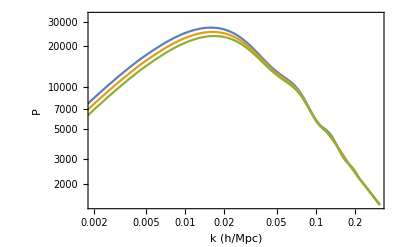

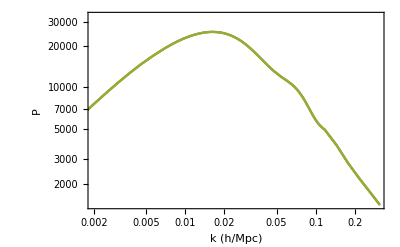

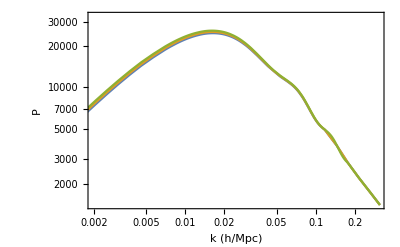

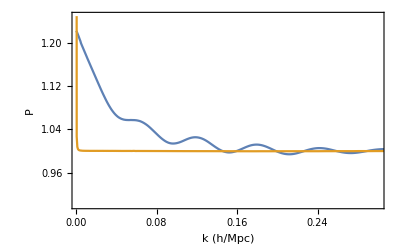

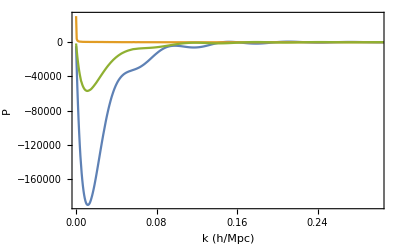

```mathematica
power29=Import[cambdir<>"camb_83922958_matterpower_z0.dat","Table"];
powerinterp29=Interpolation[power29];
power31=Import[cambdir<>"camb_06223337_matterpower_z0.dat","Table"];
powerinterp31=Interpolation[power31];
dpdΩm0=power31;
dpdΩm0[[All,2]]=1/(.31-.29)(power31[[All,2]]-power29[[All,2]]);
dpdΩm0fun=Interpolation[dpdΩm0]

(*powerOk0p01=Import[cambdir<>"camb_81668952_matterpower_z0.dat","Table"];
powerOk0m01=Import[cambdir<>"camb_24841287_matterpower_z0.dat","Table"];
*)
powerOk0p01=Import[cambdir<>"camb_57163067_matterpower_z0.dat","Table"];
powerOk0m01=Import[cambdir<>"camb_04645648_matterpower_z0.dat","Table"];
powerinterpOk0p01=Interpolation[powerOk0p01];
powerinterpOk0m01=Interpolation[powerOk0m01];
dpdΩk0=powerOk0m01;
dpdΩk0[[All,2]]=1/(.01+.01)(powerOk0p01[[All,2]]-powerOk0m01[[All,2]]);
dpdΩk0fun=Interpolation[dpdΩk0]

powerh71=Import[cambdir<>"camb_23786423_matterpower_z0.dat","Table"];
powerh69=Import[cambdir<>"camb_92156583_matterpower_z0.dat","Table"];
powerinterph71=Interpolation[powerh71];
powerinterph69=Interpolation[powerh69];
dpdh=powerh71;
dpdh[[All,2]]=1/(.71-.69)(powerh71[[All,2]]-powerh69[[All,2]]);
dpdhfun=Interpolation[dpdh]

(*power297=Import[cambdir<>"camb_83109421_matterpower_z0.dat","Table"];
powerinterp297=Interpolation[power297];
power303=Import[cambdir<>"camb_87437855_matterpower_z0.dat","Table"];
powerinterp303=Interpolation[power303];
dpdΩm0=power303;
dpdΩm0[[All,2]]=1/(.303-.297)(power303[[All,2]]-power297[[All,2]]);
dpdΩm0fun=Interpolation[dpdΩm0]*)
LogLogPlot[{powerinterp29[x],powerinterp[x],powerinterp31[x]},{x,10^-4,2},Frame->True,FrameLabel->{"k (h/Mpc)","P"},PlotRange->{{2 10^-3,.3},{1400,3.3 10^4}},FrameStyle->14]
LogLogPlot[{powerinterpOk0p01[x],powerinterp[x],powerinterpOk0m01[x]},{x,10^-4,2},Frame->True,FrameLabel->{"k (h/Mpc)","P"},PlotRange->{{2 10^-3,.3},{1400,3.3 10^4}},FrameStyle->14]
LogLogPlot[{powerinterph71[x],powerinterp[x],powerinterph69[x]},{x,10^-4,2},Frame->True,FrameLabel->{"k (h/Mpc)","P"},PlotRange->{{2 10^-3,.3},{1400,3.3 10^4}},FrameStyle->14]
Plot[{powerinterp29[x]/powerinterp31[x],powerinterpOk0p01[x]/powerinterpOk0m01[x]},{x,10^-4,2},Frame->True,FrameLabel->{"k (h/Mpc)","P"},PlotRange->{{2 10^-3,.3},{.9,1.25}},FrameStyle->14]
Plot[{dpdΩm0fun[x],dpdΩk0fun[x],dpdhfun[x]},{x,10^-4,2},Frame->True,FrameLabel->{"k (h/Mpc)","P"},PlotRange->{{2 10^-3,.3},All},FrameStyle->14]
```

Difference between derivative steps in Ωm0

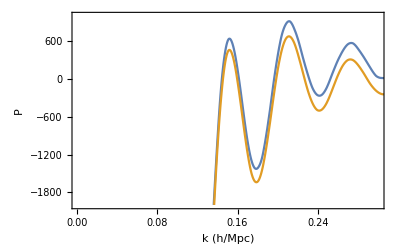

### kmin

```mathematica
kminvecΔz0p05={{0.025,0.03468},{0.075,0.01837},{0.125,0.01338},{0.175,0.01089},{0.225,0.00938},{0.275,0.00835},{0.325,0.00761},{0.375,0.00704},{0.425,0.0066},{0.475,0.00624},{0.525,0.00595}};
kminvecΔz0p1={{0.05,0.01754},{0.15,0.00943},{0.25,0.00699},{0.35,0.0058},{0.45,0.00509},{0.55,0.00462},{0.65,0.0043},{0.75,0.00406},{0.85,0.00387},{0.95,0.00373}};

kminvecLSSTΔz0p05=kminvecΔz0p05;
kminvecLSSTΔz0p1=kminvecΔz0p1;
```

### LSST number densities

```mathematica
fskyLSST=18000/(180/π)^2 1./(4π);
```

```mathematica
Cappellaro15Rate[z_]:=.21(1+z)^1.95 10^-4;
(*Dilday10Rate[z_]:=.26(1+z)^1.5 10^-4;*)

fidsnrate[z_]:=Cappellaro15Rate[z]hh^-3/(1+z); (* corrects for obsframe and Mpc/h *)
(*firstpaperRate[z_]:=.26(1+z)^2.5 10^-4;*)
Round[Map[fidsnrate[#]&,Range[.05,.75,.1]] 10^3,.0001]
Round[volLSSTbins={0.1339,0.8618,2.119,3.713,5.486,7.319,9.124,10.84} hh^3 ,.001]
```

{0.0641,0.0699,0.0757,0.0814,0.0871,0.0928,0.0985,0.1042}

{0.046,0.296,0.727,1.274,1.882,2.51,3.13,3.718}

InterpolatingFunction[…]

InterpolatingFunction[…]

InterpolatingFunction[…]

InterpolatingFunction::dmval: Input value {0.0250138} lies outside the range of data in the interpolating function. Extrapolation will be used.

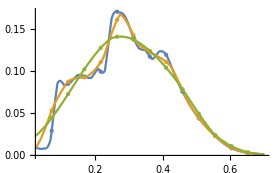

```mathematica
(*nscaling[x_]:=x^1.3;*)  (* completeness seem to increase with (t/5yr)^1.3 *)
sncompletfid=0.2;
completenessLSSTvec5y=Import["LSST\\completnessLSST5yr-Dz=0.02.txt","Table"];
completenessLSSTvec10y=Import["LSST\\completnessLSST10yr-Dz=0.02.txt","Table"];
completenessLSSTvec5yΔz0p05=Import["LSST\\completnessLSST5yr-Dz=0.05.txt","Table"];
completenessSQΔz002=Interpolation[completenessLSSTvec5y]
completenessSQΔz005=Interpolation[completenessLSSTvec5yΔz0p05]
completenessLSSTvec5yΔz0p1=Table[{zmin+.05,NIntegrate[dCO6[z]^0 completenessSQΔz005[z],{z,zmin,zmin+.1}]/NIntegrate[dCO6[z]^0,{z,zmin,zmin+.1}]},{zmin,0,.8,.1}];
completenessSQΔz01=Interpolation[completenessLSSTvec5yΔz0p1]
Plot[{completenessSQΔz002[z],completenessSQΔz005[z],completenessSQΔz01[z]},{z,.025,.7},Mesh->13,ImageSize->280]
```

```mathematica
completeness20p[z_]:=0.2;
nLSST5y20pΔz0p1=Map[5*fidsnrate[#]completeness20p[#]&,Range[.05,.75,.1]]
nLSST5ySQΔz0p1=Map[5*fidsnrate[#]completenessSQΔz01[#]&,Range[.05,.75,.1]]
nLSST5y20pΔz0p05=Map[5*fidsnrate[#]completeness20p[#]&,Range[.025,.475,.05]]
nLSST5ySQΔz0p05=Map[5*fidsnrate[#]completenessSQΔz005[#]&,Range[.025,.475,.05]]
```

```mathematica
kminvecΔz0p05={{0.025,0.03468},{0.075,0.01837},{0.125,0.01338},{0.175,0.01089},{0.225,0.00938},{0.275,0.00835},{0.325,0.00761},{0.375,0.00704},{0.425,0.0066},{0.475,0.00624},{0.525,0.00595}};
kminvecΔz0p1={{0.05,0.01754},{0.15,0.00943},{0.25,0.00699},{0.35,0.0058},{0.45,0.00509},{0.55,0.00462},{0.65,0.0043},{0.75,0.00406},{0.85,0.00387},{0.95,0.00373}};

kminvecLSSTΔz0p05=kminvecΔz0p05;
kminvecLSSTΔz0p1=kminvecΔz0p1;
```

```mathematica
EE[z_]:=√(Ωm0fid (1+z)^3+(1-Ωm0fid));
dEdz[z_]=D[EE[z], z];
d2Edz2[z_]=D[EE[z], z,z];
ff[z_]:=((Ωm0fid (1+z)^3)/EE[z]^2)^0.545;
G[zz_]:=Exp[-NIntegrate[ff[z]/(1+z),{z,0,zz}]]
```

### Approximations for d_C, f, G, etc.

```mathematica
EE[z_]:=√(Ωm0fid (1+z)^3+(1-Ωm0fid));
EEΩm0[z_,Ωm0_]:=√(Ωm0 (1+z)^3+(1-Ωm0));
EEΩm0Ωk0[z_,Ωm0_,Ωk0_]:=√(Ωm0 (1+z)^3+Ωk0 (1+z)^2+(1-Ωm0-Ωk0));
dEdz[z_]=D[EE[z], z];
d2Edz2[z_]=D[EE[z], z,z];
ff[z_]:=((Ωm0fid (1+z)^3)/EE[z]^2)^0.545;
```

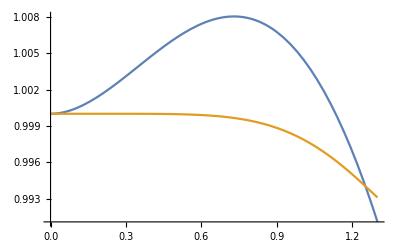

```mathematica
Clear[zz]
dCintegrandO1[z_]=Evaluate[Normal[Series[1/EE[z],{z,0,1}]]];
dCintegrandO6[z_]=Evaluate[Normal[Series[1/EE[z],{z,0,6}]]];
dC[zz_]:=NIntegrate[1/EE[z],{z,0,zz}];
dCalt[zz_]=z-dEdz[0]/2 z^2+1/6(2 dEdz[0]-d2Edz2[0])z^3;
dCO1[zz_]=Integrate[dCintegrandO1[z],{z,0,zz},Assumptions->zz>0];
dCO6[zz_]=Integrate[dCintegrandO6[z],{z,0,zz},Assumptions->zz>0];
dAO1[z_]:=dCO1[z]/(1+z);

Plot[{dCO1[z]/dC[z],dCO6[z]/dC[z]},{z,0,1.3},PlotRange->All]
```

```mathematica
G[zz_]:=Exp[-NIntegrate[ff[z]/(1+z),{z,0,zz}]]
```

int=Integrate[-1/(1+z)(((3./10) (1+z)^3)/(3/10(1+z)^3+(1-3/10)))^γ,{z,0,Z},Assumptions→{Z>0, 0<Ωm0<1}];
FullSimplify[int,{Z>0, 0<γ<1}]

1/3 0.428571^γ Gamma[γ] (Hypergeometric2F1Regularized[γ,γ,1+γ,-3/7]-(1+Z)^(3 γ) Hypergeometric2F1Regularized[γ,γ,1+γ,-3/7 (1+Z)^3])

```mathematica
ffγ[z_,γ_]:=((Ωm0fid (1+z)^3)/EE[z]^2)^γ;
Gγfull[zz_,γ_]:=Exp[-NIntegrate[ffγ[z,γ]/(1+z),{z,0,zz}]];
(* The expr. below assumes Ωm0 = 0.3 *)
Gγ[z_,γ_]:=Exp[1/3 0.42857143^γ Gamma[γ] (Hypergeometric2F1Regularized[γ,γ,1+γ,-3/7]-(1+z)^(3 γ) Hypergeometric2F1Regularized[γ,γ,1+γ,-3/7 (1+z)^3])];
fσ8[z_,σ8_,γ_]:=σ8 ffγ[z,γ]Gγ[z,γ]; 
{Gγ[.45,γfid],Gγfull[.45,γfid]}
```

{0.791722,0.791722}

### Mantz and Planck CMB plots

```mathematica
SetDirectory[NotebookDirectory[]<>"//Mantz.plots"]
```

C:\Users\Miguel Quartin\Dropbox\SNe.Pec.Velocities\Pdd.Pdv.Pvv.paper.2\fisher_matrix\github\Mantz.plots

```mathematica
mantzblue=Lighter[RGBColor[0.23,0.82,0.94],.2]
```

RGBColor[0.384, 0.856, 0.952]

```mathematica
cmb2σupper=Import["Mantz-CMB-2s-upper.csv","CSV"];
cmb2σlower=Import["Mantz-CMB-2s-lower.csv","CSV"];
cmb1σupper=Import["Mantz-CMB-1s-upper.csv","CSV"];
cmb1σlower=Import["Mantz-CMB-1s-lower.csv","CSV"];
cmbplot=ListPlot[{cmb2σupper,cmb2σlower,cmb1σupper,cmb1σlower},Joined->True,PlotStyle->Directive[Thickness[.002],Darker[mantzblue,.5]],Filling->{1->{{2},Lighter[mantzblue,.6]},3->{{4},mantzblue}}];
```

```mathematica
γlist[[;;All;;6]]
```

{-1.,-0.772,-0.544,-0.316,-0.088,0.14,0.368,0.596,0.824,1.052,1.28,1.508,1.736,1.964,2.192,2.42}

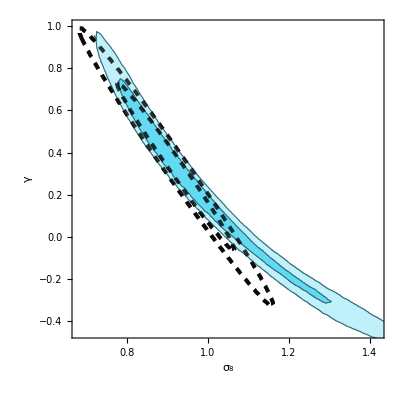

```mathematica
{σ1,σ2,ρ}={.097,.267,-.99};
FMCMB=Inverse[{{σ1^2,ρ σ1 σ2},{ρ σ1 σ2,σ2^2}}];
chisqCMB=FMCMBchisqfun[FMCMB,1.11σ8fid,Range[.68,1.42,.01],.61γfid,Range[-.45,1,.01]];
pcmbFM=lplotpriorfun[chisqCMB,{2.3,6.17(*,11.8*)},{"σ_8","γ"}];
lpCMB=Show[pcmbFM,cmbplot,pcmbFM]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Miguel Quartin\Dropbox\SNe.Pec.Velocities\Pdd.Pdv.Pvv.paper.2\fisher_matrix\github

```mathematica
(* H0, Ωm0, Ωk0 -- Planck 2018 TTTEEE, no lensing *)
CMBcov3D={{13.629651906652573,-0.23485660004504635,0.06326043013455822},{-0.23485660004504635,0.004143760912492466,-0.0011070216016933721},{0.06326043013455822,-0.0011070216016933721,0.0003035191813907464}};
CMBcov3D=CMBcov3D[[{2,3,1},{2,3,1}]];  (* re-orders to Om0, Ok0, h*)
CMBcov3D[[All,3]]*=1/100;CMBcov3D[[3,All]]*=1/100;
CMBcov3D//MatrixForm
```

(0.00414376 | -0.00110702 | -0.00234857
-0.00110702 | 0.000303519 | 0.000632604
-0.00234857 | 0.000632604 | 0.00136297)

## Choose forecast: n_δδ, n_vv, z bins & k_min

```mathematica
forecast=1; (* 0 for conservative, 1 for aggressive *)

kminfixflag=0; (* 0 for physical kmin, 1 for fixed value for all redshifts *)
Δz=0.1;zmax=0.80;
zzvec=Range[.05,zmax-Δz/2,Δz]

dCoverdH[z_]:=dCO6[z];
ΔV[z_]:=2998^3 4π fskyLSST NIntegrate[(dCoverdH[zz])^2/EE[zz],{zz,z-Δz/2,z+Δz/2}]
(*  in (Mpc/h)^3  *)
(* Conservative / Aggressive *)
(* kmin = 2π / V^(1/3) *)
kminvecΔz0p1=kminvecLSSTΔz0p1;
kminvecΔz0p05=kminvecLSSTΔz0p05;
Which[forecast==0,{area=7500,sncomplet=0.15,kminvecΔz0p05[[All,2]]*=(area/18000)^(-1/3),kminvecΔz0p1[[All,2]]*=(area/18000)^(-1/3)},
forecast==1,{area=18000,sncomplet=0.3}];
nsnfun=Interpolation[Thread[{zzvec,(sncomplet/sncompletfid) nLSST5y20pΔz0p1}],InterpolationOrder->1];
Round[ΔVvec=(area/18000)Map[ΔV,zzvec],10.^6]
```

{0.05,0.15,0.25,0.35,0.45,0.55,0.65,0.75}

{4.6×10^7,2.96×10^8,7.27×10^8,1.273×10^9,1.882×10^9,2.51×10^9,3.128×10^9,3.715×10^9}

```mathematica
NSN=ΔVvec (sncomplet/sncompletfid) nLSST5y20pΔz0p1;
NSN[[1;;5]]
Total[%]
```

{4419.,31003.,82497.9,155525.,245965.}

519410.

```mathematica
Clear[kminLSST0p1fun,kminLSST0p05fun]
kminvecΔz0p1
kminvecLSSTΔz0p1
```

{{0.05,0.01754},{0.15,0.00943},{0.25,0.00699},{0.35,0.0058},{0.45,0.00509},{0.55,0.00462},{0.65,0.0043},{0.75,0.00406},{0.85,0.00387},{0.95,0.00373}}

{{0.05,0.01754},{0.15,0.00943},{0.25,0.00699},{0.35,0.0058},{0.45,0.00509},{0.55,0.00462},{0.65,0.0043},{0.75,0.00406},{0.85,0.00387},{0.95,0.00373}}

## LSST 6×2pt FM; AP: σ_8, γ, h, Ω_m0& Ω_k0

```mathematica
bschoice=1.0;
```

```mathematica
bschoice=1.5;
```

### Preamble

```mathematica
Clear[CC2,CC3,Υ,Pmmfun]
Ωk0fid=0;
F2[z_]:=((1+z)^2-1)/(2 EE[z]^2);F3[z_]:=((1+z)^3-1)/(2 EE[z]^2);
CC2full[z_]:=((-1)/dCoverdH[z])NIntegrate[F2[zz]/EE[zz],{zz,0,z}]+(1/6)dCoverdH[z]^2;
CC3full[z_]:=((-1)/dCoverdH[z])NIntegrate[F3[zz]/EE[zz],{zz,0,z}];
(* pre-computing these factors *)
AbsoluteTiming[CC2=Interpolation[Map[{#,CC2full[#]}&,zzvec]]]
AbsoluteTiming[CC3=Interpolation[Map[{#,CC3full[#]}&,zzvec]]]
```

{0.0331125,InterpolatingFunction[…]}

{0.0340148,InterpolatingFunction[…]}

```mathematica
σδfid=4.24;σgfid=4.24;σvfid=6√2;r=10;
FMfun[case_]:=Module[{},
ngg[z_]:=r 10^-0 nsnfun[z];nggvec=Map[ngg,zzvec];
nδδ[z_]:=10^-0 nsnfun[z];nδδvec=Map[nδδ,zzvec];
nvv[z_]:=10^-0 nsnfun[z];nvvvec=Map[nvv,zzvec];
ngδ[z_]:=(0/1)Min[ngg[z],nδδ[z]] ;(* zero/half/all of the SN are in observed galaxies *)


Clear[Hr,Sδ,Sv,nPδδ,nPδv,nPvv,Cab,CabInv];
bsfid[z_]:=bschoice/G[z];    (* 1.5/G[z] or 1.0/G[z] *)
bgfid[z_]:=Piecewise[{{1.34/G[z],z<=0.3},{1.7/G[z],z>0.3}}];
bsfidvec=Map[bsfid,zzvec];
bgfidvec=Map[bgfid,zzvec];

(*Gvec=Map[G,zzvec];*)
(* fid Pmm(k) in (h/Mpc)^3*)
(*Pmmfun[k_,z_,σ8_,γ_]:=Gγ[z,γ]^2 (σ8/σ8camb)^2 powerinterp[k];*) 

(* Trick to compute derivative wrt to Ωm0, Ωk0 and h analytically *)
(*Pmmfun[k_,z_,σ8_,γ_,Ωm0_]:=Gγ[z,γ]^2 (σ8/σ8camb)^2 powerinterp[k]+(Ωm0-Ωm0fid)Gγ[z,γ]^2 (σ8/σ8camb)^2 dpdΩm0fun[k]; *)
Υ[Ωm0_,Ωk0_,h_,z_]:=1+(Ωm0-Ωm0fid) (F3[z]-2CC3[z])+(Ωk0-Ωk0fid) (F2[z]-2CC2[z])+(h-hh)3/hh;
Pmmfun[k_,z_,σ8_,γ_,Ωm0_,Ωk0_,h_,μ_]:=Gγ[z,γ]^2 (σ8/σ8camb)^2 (powerinterp[k]+(Ωm0-Ωm0fid)(dpdΩm0fun[k]+dPmmdlnk[k](μ^2 F3[z]+(μ^2-1)CC3[z]))+(Ωk0-Ωk0fid)( dpdΩk0fun[k]+dPmmdlnk[k](μ^2 F2[z]+(μ^2-1)CC2[z]))+(h-hh)(dpdhfun[k]+dPmmdlnk[k]/hh));
(*Pmmfun[k_,z_,σ8_,γ_,Ωm0_,Ωk0_,μ_]:=Gγ[z,γ]^2 (σ8/σ8camb)^2 powerinterp[k]+(Ωm0-Ωm0fid)Gγ[z,γ]^2 (σ8/σ8camb)^2 dpdΩm0fun[k];*)


(*Hr[z_,Ωm0_]:=2998^-1 EEΩm0[z,Ωm0]; *)(* in h/Mpc *)
Hr[z_,Ωm0_,Ωk0_,h_]:=2998^-1 EEΩm0Ωk0[z,Ωm0,Ωk0](h/hh); (* in h/Mpc *)

σvnonlinsq=(300/299792)^2;
σveffsq[z_,σint_]:=((Log[10]/5)σint)^2(dCoverdH[z] /(dCoverdH[z] - (1+z)/EE[z]))^2+σvnonlinsq;
(*Sδ[k_,μ_,σδ_]:=1;Sv[k_,σv_]:=1;*)

Sδ[k_,μ_,σδ_]:=Exp[-(1/4)(k μ σδ)^2]; Sv[k_,μ_,σv_]:=Exp[-(1/4)(k μ σv)^2];Sg[k_,μ_,σg_]:=Exp[-(1/4)(k μ σg)^2];

(* I now use 2 μ variables: μ and μr. This is to avoid differentiating μr by mistake. Afterall, the deriv. wrt to ln k, already performed before, result in terms which depend on μr *)
nPδδ[k_,μ_,μr_,z_,σ8_,γ_,bs_,σv_,σδ_,Ωm0_,Ωk0_,h_]:=Υ[Ωm0,Ωk0,h,z]nδδ[z]((1+(ffγ[z,γ]/bs)μ^2)^2 bs^2 Sδ[k,μ,σδ]^2 Pmmfun[k,z,σ8,γ,Ωm0,Ωk0,h,μr]+1/nδδ[z]);
nPgg[k_,μ_,μr_,z_,σ8_,γ_,bg_,σv_,σg_,Ωm0_,Ωk0_,h_]:=Υ[Ωm0,Ωk0,h,z]nδδ[z]((1+(ffγ[z,γ]/bg)μ^2)^2 bg^2 Sg[k,μ,σg]^2 Pmmfun[k,z,σ8,γ,Ωm0,Ωk0,h,μr]+1/ngg[z]);
nPδv[k_,μ_,μr_,z_,σ8_,γ_,bs_,σv_,σδ_,Ωm0_,Ωk0_,h_]:=Υ[Ωm0,Ωk0,h,z]nδδ[z](1+(ffγ[z,γ]/bs)μ^2)((Hr[z,Ωm0,Ωk0,h] μ Sv[k,μ,σv])/(k(1+z)))ffγ[z,γ] bs Sδ[k,μ,σδ]Pmmfun[k,z,σ8,γ,Ωm0,Ωk0,h,μr];
nPgv[k_,μ_,μr_,z_,σ8_,γ_,bg_,σv_,σg_,Ωm0_,Ωk0_,h_]:=Υ[Ωm0,Ωk0,h,z]nδδ[z](1+(ffγ[z,γ]/bg)μ^2)((Hr[z,Ωm0,Ωk0,h] μ Sv[k,μ,σv])/(k(1+z)))ffγ[z,γ] bg Sg[k,μ,σg]Pmmfun[k,z,σ8,γ,Ωm0,Ωk0,h,μr];
nPδg[k_,μ_,μr_,z_,σ8_,γ_,bs_,bg_,σv_,σδ_,σg_,Ωm0_,Ωk0_,h_]:=Υ[Ωm0,Ωk0,h,z]nδδ[z]((1+(ffγ[z,γ]/bs)μ^2)(1+(ffγ[z,γ]/bg)μ^2)bs bg Sδ[k,μ,σδ]Sg[k,μ,σg]Pmmfun[k,z,σ8,γ,Ωm0,Ωk0,h,μr]+ngδ[z]/(ngg[z]nδδ[z]));
nPvv[k_,μ_,μr_,z_,σ8_,γ_,σv_,σδ_,σint_,Ωm0_,Ωk0_,h_]:=Υ[Ωm0,Ωk0,h,z]nδδ[z](((Hr[z,Ωm0,Ωk0,h] μ Sv[k,μ,σv])/(k(1+z)))^2 ffγ[z,γ]^2 Pmmfun[k,z,σ8,γ,Ωm0,Ωk0,h,μr]+σveffsq[z,σint]/nvv[z]);

Which[case==0,(* vv *)
{Cab[k_,μ_,μr_,σ8_,γ_,bs_,bg_,σv_,σδ_,σg_,z_,σint_,Ωm0_,Ωk0_,h_]:={{nPvv[k,μ,μr,z,σ8,γ,σv,σδ,σint,Ωm0,Ωk0, h]}};
CabInv[k_,μ_,μr_,σ8_,γ_,bs_,bg_,σv_,σδ_,σg_,z_,σint_,Ωm0_,Ωk0_,h_]:=Inverse[Cab[k,μ,μr,σ8,γ,bs,bg,σv,σδ,σg,z,σint,Ωm0,Ωk0, h]];},
case==1,(* gg *)
{Cab[k_,μ_,μr_,σ8_,γ_,bs_,bg_,σv_,σδ_,σg_,z_,σint_,Ωm0_,Ωk0_,h_]:={{nPgg[k,μ,μr,z,σ8,γ,bg,σv,σg,Ωm0,Ωk0, h]}};
CabInv[k_,μ_,μr_,σ8_,γ_,bs_,bg_,σv_,σδ_,σg_,z_,σint_,Ωm0_,Ωk0_,h_]:=Inverse[Cab[k,μ,μr,σ8,γ,bs,bg,σv,σδ,σg,z,σint,Ωm0,Ωk0, h]];},
case==2,(* 3×2 g-s *)
{Cab[k_,μ_,μr_,σ8_,γ_,bs_,bg_,σv_,σδ_,σg_,z_,σint_,Ωm0_,Ωk0_,h_]:={{nPvv[k,μ,μr,z,σ8,γ,σv,σδ,σint,Ωm0,Ωk0, h],nPgv[k,μ,μr,z,σ8,γ,bg,σv,σg,Ωm0,Ωk0, h]},{nPgv[k,μ,μr,z,σ8,γ,bg,σv,σg,Ωm0,Ωk0, h],nPgg[k,μ,μr,z,σ8,γ,bg,σv,σg,Ωm0,Ωk0, h]}};
CabInv[k_,μ_,μr_,σ8_,γ_,bs_,bg_,σv_,σδ_,σg_,z_,σint_,Ωm0_,Ωk0_,h_]:=Inverse[Cab[k,μ,μr,σ8,γ,bs,bg,σv,σδ,σg,z,σint,Ωm0,Ωk0, h]];},
case==3,(* 6×2 *)
{Cab[k_,μ_,μr_,σ8_,γ_,bs_,bg_,σv_,σδ_,σg_,z_,σint_,Ωm0_,Ωk0_,h_]:={{nPδδ[k,μ,μr,z,σ8,γ,bs,σv,σδ,Ωm0,Ωk0, h],nPδv[k,μ,μr,z,σ8,γ,bs,σv,σδ,Ωm0,Ωk0, h],nPδg[k,μ,μr,z,σ8,γ,bs,bg,σv,σδ,σg,Ωm0,Ωk0, h]},{nPδv[k,μ,μr,z,σ8,γ,bs,σv,σδ,Ωm0,Ωk0, h],nPvv[k,μ,μr,z,σ8,γ,σv,σδ,σint,Ωm0,Ωk0, h],nPgv[k,μ,μr,z,σ8,γ,bg,σv,σg,Ωm0,Ωk0, h]},{nPδg[k,μ,μr,z,σ8,γ,bs,bg,σv,σδ,σg,Ωm0,Ωk0, h],nPgv[k,μ,μr,z,σ8,γ,bg,σv,σg,Ωm0,Ωk0, h],nPgg[k,μ,μr,z,σ8,γ,bg,σv,σg,Ωm0,Ωk0, h]}};
CabInv[k_,μ_,μr_,σ8_,γ_,bs_,bg_,σv_,σδ_,σg_,z_,σint_,Ωm0_,Ωk0_,h_]:=Inverse[Cab[k,μ,μr,σ8,γ,bs,bg,σv,σδ,σg,z,σint,Ωm0,Ωk0, h]];}
];

Print[Cab[.1,.5,.5,.83,γfid,bsfid[.1],bgfid[.1],σvfid,σδfid,σgfid,.15,.13,Ωm0fid,Ωk0fid,hh]];
Print[CabInv[.1,.5,.5,.83,γfid,bsfid[.1],bgfid[.1],σvfid,σδfid,σgfid,.15,.13,Ωm0fid,Ωk0fid,hh]];
Print[Map[Det[Cab[.1,.5,.5,.83,γfid,bsfid[.1],bgfid[#],σvfid,σδfid,σgfid,#,.13,Ωm0fid,Ωk0fid,hh]]&,zzvec]];

Clear[kr,Fbar,FMtot,FM,zz,z,FMvec];

Fbar[p1_,p2_,z_,σint_]:=multfact(1/2)du Total[Map[Tr[(D[Cab[kr,μ[Ωm0,Ωk0],#,σ8,γ,bs,bg,σv,σδ,σg,z,σint,Ωm0,Ωk0, h],p1]/.{μ[Ωm0,Ωk0]->#,Derivative[1,0][μ][Ωm0,Ωk0]->#(1-#^2)(F3[z]+CC3[z]), Derivative[0,1][μ][Ωm0,Ωk0]->#(1-#^2)(F2[z]+CC2[z])}/.{σ8->σ8fid,γ->γfid,bs->bsfid[z],bg->bgfid[z],σv->σvfid,σδ->σδfid,σg->σgfid, Ωm0->Ωm0fid, Ωk0->Ωk0fid, h-> hh}).CabInv[kr,#,#,σ8fid,γfid,bsfid[z],bgfid[z],σvfid,σδfid,σgfid,z,σint,Ωm0fid,Ωk0fid, hh].(D[Cab[kr,μ[Ωm0,Ωk0],#,σ8,γ,bs,bg,σv,σδ,σg,z,σint,Ωm0,Ωk0, h],p2]/.{μ[Ωm0,Ωk0]->#,Derivative[1,0][μ][Ωm0,Ωk0]->#(1-#^2)(F3[z]+CC3[z]), Derivative[0,1][μ][Ωm0,Ωk0]->#(1-#^2)(F2[z]+CC2[z])}/.{σ8->σ8fid,γ->γfid,bs->bsfid[z],bg->bgfid[z],σv->σvfid,σδ->σδfid,σg->σgfid, Ωm0->Ωm0fid, Ωk0->Ωk0fid, h-> hh}).CabInv[kr,#,#,σ8fid,γfid,bsfid[z],bgfid[z],σvfid,σδfid,σgfid,z,σint,Ωm0fid,Ωk0fid, hh]]&,μvec]];


kmax=0.1;
Δkfact=1;
du=1/10;
{μvec=Range[du/2,1-du/2,du]; multfact=2;};

(*{μvec=Range[-1+du/2,1-du/2,du]; multfact=1;};*)

{iσ8,iγ,iσv,iσδ,iσg,iΩm0,iΩk0,ih}=2zbins+{1,2,3,4,5,6,7,8};
AbsoluteTiming[Monitor[FMvec=
ParallelTable[
zz=zzvec[[iz]];
kmin=kminvecΔz0p1[[iz,2]];Δk=Δkfact 2π/ΔVvec[[iz]]^(1/3);
(* k starts at kmax and go down until kmin *)
kbins=Range[kmax,kmin,-Δk];kbins=Join[kbins,{kmin}];
Δklast=kbins[[-2]]-kmin; (* the last kbin is smaller in order not to go below kmin *)
kvec=MovingAverage[kbins,2]; (* central ks *)
FMlength=2zbins+8;
FMtot=Table[0,{i,FMlength},{j,FMlength}];
Do[
FM=Table[0,{i,FMlength},{j,FMlength}];
kr=kvec[[ik]];
If[ik==Length[kvec],VVk=(Δklast/Δk)((Δkfact kr^2 ΔVvec[[iz]]^(2/3))/(2π)),VVk=(Δkfact kr^2 ΔVvec[[iz]]^(2/3))/(2π)];

FM[[2iz-1,2iz-1]]=Fbar[bs,bs,zz,σintfid];
FM[[2iz-1,2iz]]=Fbar[bs,bg,zz,σintfid];
FM[[2iz-1,iσ8]]=Fbar[bs,σ8,zz,σintfid];
FM[[2iz-1,iγ]]=Fbar[bs,γ,zz,σintfid];
FM[[2iz-1,iσv]]=Fbar[bs,σv,zz,σintfid];
FM[[2iz-1,iσδ]]=Fbar[bs,σδ,zz,σintfid];
FM[[2iz-1,iσg]]=Fbar[bs,σg,zz,σintfid];
FM[[2iz-1,iΩm0]]=Fbar[bs,Ωm0,zz,σintfid];
FM[[2iz-1,iΩk0]]=Fbar[bs,Ωk0,zz,σintfid];
FM[[2iz-1,ih]]=Fbar[bs,h,zz,σintfid];

FM[[2iz,2iz]]=Fbar[bg,bg,zz,σintfid];
FM[[2iz,iσ8]]=Fbar[bg,σ8,zz,σintfid];
FM[[2iz,iγ]]=Fbar[bg,γ,zz,σintfid];
FM[[2iz,iσv]]=Fbar[bg,σv,zz,σintfid];
FM[[2iz,iσδ]]=Fbar[bg,σδ,zz,σintfid];
FM[[2iz,iσg]]=Fbar[bg,σg,zz,σintfid];
FM[[2iz,iΩm0]]=Fbar[bg,Ωm0,zz,σintfid];
FM[[2iz,iΩk0]]=Fbar[bg,Ωk0,zz,σintfid];
FM[[2iz,ih]]=Fbar[bg,h,zz,σintfid];

FM[[iσ8,iσ8]]=Fbar[σ8,σ8,zz,σintfid];
FM[[iσ8,iγ]]=Fbar[σ8,γ,zz,σintfid];
FM[[iσ8,iσv]]=Fbar[σ8,σv,zz,σintfid];
FM[[iσ8,iσδ]]=Fbar[σ8,σδ,zz,σintfid];
FM[[iσ8,iσg]]=Fbar[σ8,σg,zz,σintfid];
FM[[iσ8,iΩm0]]=Fbar[σ8,Ωm0,zz,σintfid];
FM[[iσ8,iΩk0]]=Fbar[σ8,Ωk0,zz,σintfid];
FM[[iσ8,ih]]=Fbar[σ8,h,zz,σintfid];

FM[[iγ,iγ]]=Fbar[γ,γ,zz,σintfid];
FM[[iγ,iσv]]=Fbar[γ,σv,zz,σintfid];
FM[[iγ,iσδ]]=Fbar[γ,σδ,zz,σintfid];
FM[[iγ,iσg]]=Fbar[γ,σg,zz,σintfid];
FM[[iγ,iΩm0]]=Fbar[γ,Ωm0,zz,σintfid];
FM[[iγ,iΩk0]]=Fbar[γ,Ωk0,zz,σintfid];
FM[[iγ,ih]]=Fbar[γ,h,zz,σintfid];

FM[[iσv,iσv]]=Fbar[σv,σv,zz,σintfid];
FM[[iσv,iσδ]]=Fbar[σv,σδ,zz,σintfid];
FM[[iσv,iσg]]=Fbar[σv,σg,zz,σintfid];
FM[[iσv,iΩm0]]=Fbar[σv,Ωm0,zz,σintfid];
FM[[iσv,iΩk0]]=Fbar[σv,Ωk0,zz,σintfid];
FM[[iσv,ih]]=Fbar[σv,h,zz,σintfid];
FM[[iσδ,iσδ]]=Fbar[σδ,σδ,zz,σintfid];
FM[[iσδ,iσg]]=Fbar[σδ,σg,zz,σintfid];
FM[[iσδ,iΩm0]]=Fbar[σδ,Ωm0,zz,σintfid];
FM[[iσδ,iΩk0]]=Fbar[σδ,Ωk0,zz,σintfid];
FM[[iσδ,ih]]=Fbar[σδ,h,zz,σintfid];
FM[[iσg,iσg]]=Fbar[σg,σg,zz,σintfid];
FM[[iσg,iΩm0]]=Fbar[σg,Ωm0,zz,σintfid];
FM[[iσg,iΩk0]]=Fbar[σg,Ωk0,zz,σintfid];
FM[[iσg,ih]]=Fbar[σg,h,zz,σintfid];
FM[[iΩm0,iΩm0]]=Fbar[Ωm0,Ωm0,zz,σintfid];
FM[[iΩm0,iΩk0]]=Fbar[Ωm0,Ωk0,zz,σintfid];
FM[[iΩm0,ih]]=Fbar[Ωm0,h,zz,σintfid];
FM[[iΩk0,iΩk0]]=Fbar[Ωk0,Ωk0,zz,σintfid];
FM[[iΩk0,ih]]=Fbar[Ωk0,h,zz,σintfid];
FM[[ih,ih]]=Fbar[h,h,zz,σintfid];

(* symmetrizes the FM assuming empty elements are zero *)
FM=FM+Transpose[FM]-DiagonalMatrix[Diagonal[FM]]; 

FMtot+=VVk FM;
,{ik,Length[kvec]}];
FMtot
,{iz,1,zbins}];,{iz,ik,Length[kvec]}]];
Print[FMvec[[1]]//MatrixForm];
]
```

## Constant bias in each bin: b(z)

```mathematica
FMdir="FMs//";
```

### FM for σ_8 × γ, b(z), P_δδ, P_δv, P_vv

Parameter order:
 bs1,bg1,..., bsn,bgn, σ8, γ, σv, σδ, σg

```mathematica
CloseKernels[];
```

```mathematica
{bschoice,forecast,r}
bsfid[z_]:=bschoice/G[z];    (* 1.5/G[z] or 1.0/G[z] *)
bgfid[z_]:=Piecewise[{{1.34/G[z],z<=0.3},{1.7/G[z],z>0.3}}];
bsfidvec=Map[bsfid,zzvec];
bgfidvec=Map[bgfid,zzvec];
bsstring=ToString[DecimalForm[bschoice,{2,1}]];
rstring=ToString[r];
If[forecast==0,{forecaststr="-cons",zbins=4},{forecaststr="-aggr",zbins=7}];
forecast
CloseKernels[];
LaunchKernels[zbins];
relσb=.5;relσσ=.5;relσh=.5;
FMprior=DiagonalMatrix[
Flatten[Join[Table[{(bsfidvec[[iz]] relσb)^-2,(bgfidvec[[iz]]relσb)^-2},{iz,1,zbins}],{(σ8fid 1000)^-2,(γfid 1000)^-2,(σvfid relσσ)^-2,(σδfid relσσ)^-2,(σδfid relσσ)^-2,(Ωm0fid 1000)^-2,(.5)^-2,(hh relσh)^-2}]]
];
Print[Dimensions[FMprior]];
Print[Diagonal[FMprior]];
```

{1.,0,10}

0

{16,16}

{3.79714,2.11469,3.41984,1.90456,3.08026,1.71545,2.7769,0.960867,1.45159×10^-6,3.36672×10^-6,0.0555556,0.222499,0.222499,0.0000111111,4.,8.16327}

```mathematica
(* Run the desired case *)
```

```mathematica
AbsoluteTiming[FMfun[0]]
```

```mathematica
AbsoluteTiming[FMfun[1]]
```

```mathematica
AbsoluteTiming[FMfun[2]]
```

```mathematica
AbsoluteTiming[FMfun[3]]
```

### Importing FMs

```mathematica
CMBcov3D
```

{{0.00414376,-0.00110702,-0.00234857},{-0.00110702,0.000303519,0.000632604},{-0.00234857,0.000632604,0.00136297}}

```mathematica
{zbinmin,zbinmax}={1,4};
bschoice=1.0;
bsstring=ToString[DecimalForm[bschoice,{2,1}]];{iσ8,iγ,iσv,iσδ,iσg,iΩm0,iΩk0,ih}=2zbinmax+{1,2,3,4,5,6,7,8};
paramvec={iσ8,iγ,ih,iΩm0,iΩk0(*,iσv,iσδ,iσg*)};
FM6x2 =ToExpression[Import[FMdir<>"FM-6x2-AP-r10-phi0-b"<>ToString[bsstring]<>"-cons-kmax01-zmax04.tab","List"]];
FM3x2 =ToExpression[Import[FMdir<>"FM-3x2gs-AP-r10-phi0-b"<>ToString[bsstring]<>"-cons-kmax01-zmax04.tab","List"]];
FMgg=ToExpression[Import[FMdir<>"FM-Pgg-AP-r10-phi0-b"<>ToString[bsstring]<>"-cons-kmax01-zmax04.tab","List"]];
FMvv =ToExpression[Import[FMdir<>"FM-Pvv-AP-phi0-b"<>ToString[bsstring]<>"-cons-kmax01-zmax04.tab","List"]];
bsfid[z_]:=bschoice/G[z];    (* 1.5/G[z] or 1.0/G[z] *)
bgfid[z_]:=Piecewise[{{1.34/G[z],z<=0.3},{1.7/G[z],z>0.3}}];
bsfidvec=Map[bsfid,zzvec];bgfidvec=Map[bgfid,zzvec];
relσb=.5;relσσ=.5;σΩm0prior=.5;relσh=2;
FMprior=DiagonalMatrix[
Flatten[Join[Table[{(bsfidvec[[iz]] relσb)^-2,(bgfidvec[[iz]]relσb)^-2},{iz,1,zbinmax}],{(σ8fid 1000)^-2,(γfid 1000)^-2,(σvfid relσσ)^-2,(σδfid relσσ)^-2,(σδfid relσσ)^-2,(σΩm0prior)^-2,(σΩm0prior)^-2,(hh relσh)^-2}]]
];
FMCMBlong=DiagonalMatrix[Table[0,{Length[FMprior]}]];
FMCMBlong[[iσ8;;iγ,iσ8;;iγ]]=FMCMB;
FMCMBlong[[iΩm0;;ih,iΩm0;;ih]]=Inverse[CMBcov3D];
Dimensions[FMprior]
Dimensions[FM3x2]
Round[FoM1=Det[ Inverse[Inverse[Total[FMgg,{1}]+FMprior][[iσ8;;iγ,iσ8;;iγ]]]]^(1/2),1]
Round[FoM2=Det[Inverse[Inverse[Total[FM3x2,{1}]+FMprior][[iσ8;;iγ,iσ8;;iγ]]]]^(1/2),1]
Round[FoM3=Det[Inverse[Inverse[Total[FM6x2,{1}]+FMprior][[iσ8;;iγ,iσ8;;iγ]]]]^(1/2),1]
Round[{FoM3/FoM2,FoM3/FoM1},.01]
Round[(Diagonal[Inverse[(Total[FM6x2,{1}]+FMprior)]]^(1/2))[[paramvec]],.001]
Round[(Diagonal[Inverse[(Total[FM6x2,{1}]+FMprior+FMCMBlong)]]^(1/2))[[paramvec]],.0001]
```

{16,16}

{4,16,16}

39

67

91

{1.36,2.34}

{0.105,0.188,0.039,0.015,0.264}

{0.0218,0.0574,0.0072,0.0099,0.0037}

```mathematica
Join[Diagonal[Inverse[FMCMB]]^(1/2),Diagonal[CMBcov3D]^(1/2)]
```

{0.097,0.267,0.0643721,0.0174218,0.0369184}

```mathematica
{zbinmin,zbinmax}={1,4};
bschoice=1.0;
bsstring=ToString[DecimalForm[bschoice,{2,1}]];{iσ8,iγ,iσv,iσδ,iσg,iΩm0,iΩk0,ih}=2zbinmax+{1,2,3,4,5,6,7,8};
FM6x2 =ToExpression[Import[FMdir<>"FM-6x2-AP-r100-phi0-b"<>ToString[bsstring]<>"-cons-kmax01-zmax04.tab","List"]];
FM3x2 =ToExpression[Import[FMdir<>"FM-3x2gs-AP-r100-phi0-b"<>ToString[bsstring]<>"-cons-kmax01-zmax04.tab","List"]];
FMgg=ToExpression[Import[FMdir<>"FM-Pgg-AP-r100-phi0-b"<>ToString[bsstring]<>"-cons-kmax01-zmax04.tab","List"]];
FMvv =ToExpression[Import[FMdir<>"FM-Pvv-AP-phi0-b"<>ToString[bsstring]<>"-cons-kmax01-zmax04.tab","List"]];
bsfid[z_]:=bschoice/G[z];    (* 1.5/G[z] or 1.0/G[z] *)
bgfid[z_]:=Piecewise[{{1.34/G[z],z<=0.3},{1.7/G[z],z>0.3}}];
bsfidvec=Map[bsfid,zzvec];bgfidvec=Map[bgfid,zzvec];
relσb=.5;relσσ=.5;σΩm0prior=.5;relσh=.7;
FMprior=DiagonalMatrix[
Flatten[Join[Table[{(bsfidvec[[iz]] relσb)^-2,(bgfidvec[[iz]]relσb)^-2},{iz,1,zbinmax}],{(σ8fid 1000)^-2,(γfid 1000)^-2,(σvfid relσσ)^-2,(σδfid relσσ)^-2,(σδfid relσσ)^-2,(σΩm0prior)^-2,(σΩm0prior)^-2,(hh relσh)^-2}]]
];
Dimensions[FMprior]
Dimensions[FM3x2]
Round[FoM1=Det[ Inverse[Inverse[Total[FMgg,{1}]+FMprior][[iσ8;;iγ,iσ8;;iγ]]]]^(1/2),1]
Round[FoM2=Det[Inverse[Inverse[Total[FM3x2,{1}]+FMprior][[iσ8;;iγ,iσ8;;iγ]]]]^(1/2),1]
Round[FoM3=Det[Inverse[Inverse[Total[FM6x2,{1}]+FMprior][[iσ8;;iγ,iσ8;;iγ]]]]^(1/2),1]
Round[{FoM3/FoM2,FoM3/FoM1},.01]
```

{16,16}

{4,16,16}

43

69

95

{1.36,2.2}

```mathematica
{zbinmin,zbinmax}={1,4};
bschoice=1.5;
bsstring=ToString[DecimalForm[bschoice,{2,1}]];{iσ8,iγ,iσv,iσδ,iσg,iΩm0,iΩk0,ih}=2zbinmax+{1,2,3,4,5,6,7,8};
FM6x2 =ToExpression[Import[FMdir<>"FM-6x2-AP-r10-phi0-b"<>ToString[bsstring]<>"-cons-kmax01-zmax04.tab","List"]];
FM3x2 =ToExpression[Import[FMdir<>"FM-3x2gs-AP-r10-phi0-b"<>ToString[bsstring]<>"-cons-kmax01-zmax04.tab","List"]];
FMgg=ToExpression[Import[FMdir<>"FM-Pgg-AP-r10-phi0-b"<>ToString[bsstring]<>"-cons-kmax01-zmax04.tab","List"]];
FMvv =ToExpression[Import[FMdir<>"FM-Pvv-AP-phi0-b"<>ToString[bsstring]<>"-cons-kmax01-zmax04.tab","List"]];
bsfid[z_]:=bschoice/G[z];    (* 1.5/G[z] or 1.0/G[z] *)
bgfid[z_]:=Piecewise[{{1.34/G[z],z<=0.3},{1.7/G[z],z>0.3}}];
bsfidvec=Map[bsfid,zzvec];bgfidvec=Map[bgfid,zzvec];
relσb=.5;relσσ=.5;σΩm0prior=.5;relσh=.7;
FMprior=DiagonalMatrix[
Flatten[Join[Table[{(bsfidvec[[iz]] relσb)^-2,(bgfidvec[[iz]]relσb)^-2},{iz,1,zbinmax}],{(σ8fid 1000)^-2,(γfid 1000)^-2,(σvfid relσσ)^-2,(σδfid relσσ)^-2,(σδfid relσσ)^-2,(σΩm0prior)^-2,(σΩm0prior)^-2,(hh relσh)^-2}]]
];
Dimensions[FMprior]
Dimensions[FM3x2]
Round[FoM1=Det[ Inverse[Inverse[Total[FMgg,{1}]+FMprior][[iσ8;;iγ,iσ8;;iγ]]]]^(1/2),1]
Round[FoM2=Det[Inverse[Inverse[Total[FM3x2,{1}]+FMprior][[iσ8;;iγ,iσ8;;iγ]]]]^(1/2),1]
Round[FoM3=Det[Inverse[Inverse[Total[FM6x2,{1}]+FMprior][[iσ8;;iγ,iσ8;;iγ]]]]^(1/2),1]
Round[{FoM3/FoM2,FoM3/FoM1},.01]
```

{16,16}

{4,16,16}

40

66

86

{1.31,2.14}

```mathematica
{zbinmin,zbinmax}={1,7};
bschoice=1.0;rstring="10";
bsstring=ToString[DecimalForm[bschoice,{2,1}]];{iσ8,iγ,iσv,iσδ,iσg,iΩm0,iΩk0,ih}=2zbinmax+{1,2,3,4,5,6,7,8};
paramvec={iσ8,iγ,ih,iΩm0,iΩk0(*,iσv,iσδ,iσg*)};
FM6x2 =ToExpression[Import[FMdir<>"FM-6x2-AP-r"<>rstring<>"-phi0-b"<>ToString[bsstring]<>"-aggr-kmax01-zmax07.tab","List"]];
FM3x2 =ToExpression[Import[FMdir<>"FM-3x2gs-AP-r"<>rstring<>"-phi0-b"<>ToString[bsstring]<>"-aggr-kmax01-zmax07.tab","List"]];
FMgg=ToExpression[Import[FMdir<>"FM-Pgg-AP-r"<>rstring<>"-phi0-b"<>ToString[bsstring]<>"-aggr-kmax01-zmax07.tab","List"]];
FMvv =ToExpression[Import[FMdir<>"FM-Pvv-AP-phi0-b"<>ToString[bsstring]<>"-aggr-kmax01-zmax07.tab","List"]];
Dimensions[FM6x2]
bsfid[z_]:=bschoice/G[z];    (* 1.5/G[z] or 1.0/G[z] *)
bgfid[z_]:=Piecewise[{{1.34/G[z],z<=0.3},{1.7/G[z],z>0.3}}];
bsfidvec=Map[bsfid,zzvec];bgfidvec=Map[bgfid,zzvec];
(*relσb=.25;relσσ=.25;*)
relσb=.5;relσσ=.5;σΩm0prior=.5;relσh=.5;
FMprior=DiagonalMatrix[
Flatten[Join[Table[{(bsfidvec[[iz]] relσb)^-2,(bgfidvec[[iz]]relσb)^-2},{iz,1,zbinmax}],{(σ8fid 1000)^-2,(γfid 1000)^-2,(σvfid relσσ)^-2,(σδfid relσσ)^-2,(σδfid relσσ)^-2,(σΩm0prior)^-2,(σΩm0prior)^-2,(hh relσh)^-2}]]
];
FMCMBlong=DiagonalMatrix[Table[0,{Length[FMprior]}]];
FMCMBlong[[iσ8;;iγ,iσ8;;iγ]]=FMCMB;
FMCMBlong[[iΩm0;;ih,iΩm0;;ih]]=Inverse[CMBcov3D];
Dimensions[FMprior]
Diagonal[FMprior];
Round[FoM1=Det[ Inverse[Inverse[Total[FMgg,{1}]+FMprior][[iσ8;;iγ,iσ8;;iγ]]]]^(1/2),1]
Round[FoM2=Det[Inverse[Inverse[Total[FM3x2,{1}]+FMprior][[iσ8;;iγ,iσ8;;iγ]]]]^(1/2),1]
Round[FoM3=Det[Inverse[Inverse[Total[FM6x2,{1}]+FMprior][[iσ8;;iγ,iσ8;;iγ]]]]^(1/2),1]
Round[{FoM3/FoM2,FoM3/FoM1},.01]
Round[(Diagonal[Inverse[(Total[FM6x2,{1}]+FMprior)]]^(1/2))[[paramvec]],.0001]
Round[(Diagonal[Inverse[(Total[FM6x2,{1}]+FMprior+FMCMBlong)]]^(1/2))[[paramvec]],.0001]
```

{7,22,22}

{22,22}

240

460

588

{1.28,2.45}

{0.0356,0.0672,0.0125,0.0047,0.0737}

{0.013,0.0322,0.0045,0.0036,0.0028}

```mathematica
{zbinmin,zbinmax}={1,7};
bschoice=1.0;rstring="100";
bsstring=ToString[DecimalForm[bschoice,{2,1}]];{iσ8,iγ,iσv,iσδ,iσg,iΩm0,iΩk0,ih}=2zbinmax+{1,2,3,4,5,6,7,8};
FM6x2 =ToExpression[Import[FMdir<>"FM-6x2-AP-r"<>rstring<>"-phi0-b"<>ToString[bsstring]<>"-aggr-kmax01-zmax07.tab","List"]];
FM3x2 =ToExpression[Import[FMdir<>"FM-3x2gs-AP-r"<>rstring<>"-phi0-b"<>ToString[bsstring]<>"-aggr-kmax01-zmax07.tab","List"]];
FMgg=ToExpression[Import[FMdir<>"FM-Pgg-AP-r"<>rstring<>"-phi0-b"<>ToString[bsstring]<>"-aggr-kmax01-zmax07.tab","List"]];
FMvv =ToExpression[Import[FMdir<>"FM-Pvv-AP-phi0-b"<>ToString[bsstring]<>"-aggr-kmax01-zmax07.tab","List"]];
Dimensions[FM6x2]
bsfid[z_]:=bschoice/G[z];    (* 1.5/G[z] or 1.0/G[z] *)
bgfid[z_]:=Piecewise[{{1.34/G[z],z<=0.3},{1.7/G[z],z>0.3}}];
bsfidvec=Map[bsfid,zzvec];bgfidvec=Map[bgfid,zzvec];
(*relσb=.25;relσσ=.25;*)
relσb=.5;relσσ=.5;σΩm0prior=.5;relσh=.5;
FMprior=DiagonalMatrix[
Flatten[Join[Table[{(bsfidvec[[iz]] relσb)^-2,(bgfidvec[[iz]]relσb)^-2},{iz,1,zbinmax}],{(σ8fid 1000)^-2,(γfid 1000)^-2,(σvfid relσσ)^-2,(σδfid relσσ)^-2,(σδfid relσσ)^-2,(σΩm0prior)^-2,(σΩm0prior)^-2,(hh relσh)^-2}]]
];
Dimensions[FMprior]
Diagonal[FMprior];
Round[FoM1=Det[ Inverse[Inverse[Total[FMgg,{1}]+FMprior][[iσ8;;iγ,iσ8;;iγ]]]]^(1/2),1]
Round[FoM2=Det[Inverse[Inverse[Total[FM3x2,{1}]+FMprior][[iσ8;;iγ,iσ8;;iγ]]]]^(1/2),1]
Round[FoM3=Det[Inverse[Inverse[Total[FM6x2,{1}]+FMprior][[iσ8;;iγ,iσ8;;iγ]]]]^(1/2),1]
Round[{FoM3/FoM2,FoM3/FoM1},.01]
```

{7,22,22}

{22,22}

251

549

692

{1.26,2.76}

```mathematica
{zbinmin,zbinmax}={1,7};
bschoice=1.5;rstring="10";
bsstring=ToString[DecimalForm[bschoice,{2,1}]];
FM6x2 =ToExpression[Import[FMdir<>"FM-6x2-AP-r"<>rstring<>"-phi0-b"<>ToString[bsstring]<>"-aggr-kmax01-zmax07.tab","List"]];
FM3x2 =ToExpression[Import[FMdir<>"FM-3x2gs-AP-r"<>rstring<>"-phi0-b"<>ToString[bsstring]<>"-aggr-kmax01-zmax07.tab","List"]];
FMgg=ToExpression[Import[FMdir<>"FM-Pgg-AP-r"<>rstring<>"-phi0-b"<>ToString[bsstring]<>"-aggr-kmax01-zmax07.tab","List"]];
FMvv =ToExpression[Import[FMdir<>"FM-Pvv-AP-phi0-b"<>ToString[bsstring]<>"-aggr-kmax01-zmax07.tab","List"]];
Dimensions[FM6x2]
bsfid[z_]:=bschoice/G[z];    (* 1.5/G[z] or 1.0/G[z] *)
bgfid[z_]:=Piecewise[{{1.34/G[z],z<=0.3},{1.7/G[z],z>0.3}}];
bsfidvec=Map[bsfid,zzvec];bgfidvec=Map[bgfid,zzvec];
(*relσb=.25;relσσ=.25;*)
relσb=.5;relσσ=.5;σΩm0prior=.5;relσh=.5;
FMprior=DiagonalMatrix[
Flatten[Join[Table[{(bsfidvec[[iz]] relσb)^-2,(bgfidvec[[iz]]relσb)^-2},{iz,1,zbinmax}],{(σ8fid 1000)^-2,(γfid 1000)^-2,(σvfid relσσ)^-2,(σδfid relσσ)^-2,(σδfid relσσ)^-2,(σΩm0prior)^-2,(σΩm0prior)^-2,(hh relσh)^-2}]]
];
Dimensions[FMprior]
Diagonal[FMprior];
Round[FoM1=Det[ Inverse[Inverse[Total[FMgg,{1}]+FMprior][[iσ8;;iγ,iσ8;;iγ]]]]^(1/2),1]
Round[FoM2=Det[Inverse[Inverse[Total[FM3x2,{1}]+FMprior][[iσ8;;iγ,iσ8;;iγ]]]]^(1/2),1]
Round[FoM3=Det[Inverse[Inverse[Total[FM6x2,{1}]+FMprior][[iσ8;;iγ,iσ8;;iγ]]]]^(1/2),1]
Round[{FoM3/FoM2,FoM3/FoM1},.01]
```

{7,22,22}

{22,22}

240

460

517

{1.13,2.15}

### Results and Plots

```mathematica
paramvec={iσ8,iγ,ih,iΩm0,iΩk0(*,iσv,iσδ,iσg*)};
Round[(Diagonal[Inverse[(Total[FMvv,{1}]+FMprior)]]^(1/2))[[paramvec]],.0001]
Round[(Diagonal[Inverse[(Total[FMgg,{1}]+FMprior)]]^(1/2))[[paramvec]],.0001]
Round[(Diagonal[Inverse[(Total[FM3x2,{1}]+FMprior)]]^(1/2))[[paramvec]],.0001]
Round[(Diagonal[Inverse[(Total[FM6x2,{1}]+FMprior)]]^(1/2))[[paramvec]],.0001]
```

{1.4701,0.977,0.5619,0.2079,0.4987}

{0.1541,0.2914,0.0412,0.0188,0.3331}

{0.1327,0.2208,0.0395,0.0153,0.2703}

{0.1045,0.1878,0.0392,0.0152,0.2643}

```mathematica
{iσ8,iγ,iσv,iσδ,iσg,iΩm0,iΩk0,ih}=2zbinmax+{1,2,3,4,5,6,7,8};
pstringvec=Join[Table["",{2zbinmax}],{"σ_8","γ","σv","σδ","σg","Ω_m0","Ω_k0","h"}];
pminmax=Join[Table[{0,1},{2zbinmax}],{{.18,1.48},{-.6,1.7},{0,1},{0,1},{0,1},{.24,.36},{-1.3,1.3},{.52,.88}}];
pminmax=Join[Table[{0,1},{2zbinmax}],{{0,1.68},{-.9,2.0},{0,1},{0,1},{0,1},{.24,.36},{-1.3,1.3},{.52,.88}}];
cplotfun[p1fid_,ip1_,p2fid_,ip2_,npoints_]:=Module[{},
pstring={pstringvec[[ip1]],pstringvec[[ip2]]};
(*Print[zbinmax];*)
(*Print[Round[Diagonal[Inverse[Total[FM6x2,{1}]]]^(1/2),.001]];*)
tickstab1=Table[.1ix,{ix,1,18}];
tickstab2=Table[If[Mod[ix,4]==2,DecimalForm[.1ix,{2,1}],""],{ix,1,18}];
tickstab1Om0=Table[.01ix,{ix,1,40}];
tickstab2Om0=Table[If[Mod[ix,4]==2,DecimalForm[.01ix,{2,2}],""],{ix,1,40}];

If[{ip1,ip2}=={iσ8,iγ},myticks=Thread[{tickstab1,tickstab2}],myticks=Automatic];
(*If[ip1==iΩm0,myticks=Thread[{tickstab1Om0,tickstab2Om0}],myticks=Automatic];*)
plottab1=Table[
If[iz==zbinmax+1,{z1,z2}={1,zbinmax},{z1,z2}={iz,iz}];

{p1min,p1max}=pminmax[[ip1]];
{p2min,p2max}=pminmax[[ip2]];

p1list=Range[p1min,p1max,(p1max-p1min)/npoints];
p2list=Range[p2min,p2max,(p2max-p2min)/npoints];
p1listzoom=Range[.6,1.06,(1.06-.6)/(2npoints)];
p2listzoom=Range[.3,.8,(.8-.3)/(2npoints)];

prange={{p1min,p1max},{p2min,p2max}};

chisqvv=FMmargchisqfun[FMvv,z1,z2,ip1,p1fid,p1list,ip2,p2fid,p2list];
chisq3x2=FMmargchisqfun[FM3x2,z1,z2,ip1,p1fid,p1list,ip2,p2fid,p2list];
chisqdd=FMmargchisqfun[FMgg,z1,z2,ip1,p1fid,p1list,ip2,p2fid,p2list];
chisq6x2=FMmargchisqfun[FM6x2,z1,z2,ip1,p1fid,p1list,ip2,p2fid,p2list];

chisqfull=FMmargchisqfun[FM6x2,z1,z2,ip1,p1fid,p1listzoom,ip2,p2fid,p2listzoom];
chisqCMB=FMCMBchisqfun[FMCMB,1.11σ8fid,p1listzoom,.61γfid,p2listzoom];
chisqfull[[All,3]]+=chisqCMB[[All,3]];chisqfull[[All,3]]-=Min[chisqfull[[All,3]]];


lpdd=lplotddfun[chisqdd,{2.3,6.17,11.8},pstring];
lpvv=lplotvvfun[chisqvv,{2.3,6.17,11.8},pstring];
lp3x2=lplotfullfun[chisq3x2,{2.3,6.17,11.8},pstring];
lp6x2=lplot6x2fun[chisq6x2,{2.3,6.17,11.8},pstring];
lpfull=lplotcmbfun[chisqfull,{2.3,6.17},pstring];

(*pos1={.74p1max-.32,.07};{row={0,-.27},pos2=pos1+row,pos3=pos2+row,pos4=pos3+row,pos5=pos4+row};
Δpos={.39+.03,.06};square={.06,.11};style=20;*)
pos1={.55,.34+.075};{row={0,-.075},pos2=pos1+row,pos3=pos2+row,pos4=pos3+row,pos5=pos4+row,pos6=pos5+row};
Δpos={.23,.02};square={.033,.033};style=19;

rect[pos_]:=Rectangle[Scaled[pos],Scaled[pos+square]];
If[iz==1,s3=Show[lpvv,lpdd,lp3x2,lp6x2,Graphics[Text[Style["z_bin="<>ToString[zzvec[[iz]]],21],{p1min+.2p1max,.88p2max}]],PlotRange->prange],
If[iz==zbinmax+1,
If[{ip1,ip2}=={iσ8,iγ},
s3=Show[lpvv,lpdd,lp3x2,lp6x2,cmbplot,lpfull,Graphics[Text[Style["z ∈ [0, "<>ToString[zbinmax/10.]<>"]",21],Scaled[{.25,.91}]]],Graphics[{color6x2,rect[pos1],colorfull,rect[pos2],colordd,rect[pos3],Darker[colorvv,.3],rect[pos4],mantzblue,rect[pos5],colorvvold,rect[pos6],
Black,Text[Style["6x2 g-s-s",style],Scaled[pos1+Δpos]],Text[Style["3x2 g-s    ",style],Scaled[pos2+Δpos]],Text[Style["1x2 gals δ ",style],Scaled[pos3+Δpos+{.01,0}]],Text[Style["1x2 SN v  ",style],Scaled[pos4+Δpos]],Text[Style["CMB        ",style],Scaled[pos5+Δpos]],
Text[Style["6x2+CMB",style],Scaled[pos6+Δpos]]}],
PlotRange->prange,FrameTicks->{{Automatic,Automatic},{Thread[{tickstab1,tickstab2}],Automatic}}],s3=Show[lpvv,lpdd,lp3x2,lp6x2,Graphics[Text[Style["z ∈ [0, "<>ToString[zbinmax/10.]<>"]",21],Scaled[{.25,.91}](*{p1min+.24p1max,.88p2max}*)]],Graphics[{color6x2,rect[pos2],colorfull,rect[pos3],colordd,rect[pos4],Darker[colorvv,.3],rect[pos5],
Black,Text[Style["6x2 g-s-s",style],Scaled[pos2+Δpos]],Text[Style["3x2 g-s    ",style],Scaled[pos3+Δpos]],Text[Style["1x2 gals δ ",style],Scaled[pos4+Δpos+{.01,0}]],Text[Style["1x2 SN v  ",style],Scaled[pos5+Δpos]]}],
PlotRange->prange,FrameTicks->{{Automatic,Automatic},{myticks,Automatic}}]],
s3=Show[lpvv,lpdd,lp3x2,lp6x2,Graphics[Text[Style["z_bin="<>ToString[zzvec[[iz]]],21],{p1min+.2p1max,.88p2max}]],PlotRange->prange,FrameTicks->{{Automatic,Automatic},{myticks,Automatic}}(*,PlotLabel-> "b(z), marg. all, kmax=0.1",LabelStyle->15*)]]],
{iz,1,zbinmax+1}];
s3
]
```

```mathematica
Dimensions[chisqCMB]
```

{7205,3}

#### Bias plots

```mathematica
(* bs and bg marg. errors, respectively *)
Round[σbs=Diagonal[Inverse[(Total[FM6x2,{1}]+FMprior)][[1;;2zbinmax;;2,1;;2zbinmax;;2]]]^(1/2),.001]
Round[σbg=Diagonal[Inverse[(Total[FM6x2,{1}]+FMprior)][[2;;2zbinmax;;2,2;;2zbinmax;;2]]]^(1/2),.001]
Round[σbs3x2=Diagonal[Inverse[(Total[FM3x2,{1}]+FMprior)][[1;;2zbinmax;;2,1;;2zbinmax;;2]]]^(1/2),.001]
Round[σbg3x2=Diagonal[Inverse[(Total[FM3x2,{1}]+FMprior)][[2;;2zbinmax;;2,2;;2zbinmax;;2]]]^(1/2),.001]
Round[σbs1x2=Diagonal[Inverse[(Total[FMgg,{1}]+FMprior)][[1;;2zbinmax;;2,1;;2zbinmax;;2]]]^(1/2),.001]
Round[σbg1x2=Diagonal[Inverse[(Total[FMgg,{1}]+FMprior)][[2;;2zbinmax;;2,2;;2zbinmax;;2]]]^(1/2),.001]
```

{0.065,0.05,0.053,0.058,0.064,0.071,0.077}

{0.07,0.065,0.071,0.098,0.108,0.118,0.127}

{0.513,0.541,0.57,0.6,0.632,0.664,0.697}

{0.08,0.078,0.085,0.118,0.129,0.14,0.152}

{0.513,0.541,0.57,0.6,0.632,0.664,0.697}

{0.088,0.091,0.104,0.148,0.166,0.184,0.201}

```mathematica
σbg/bgfidvec[[1;;4]]
σbs/bsfidvec[[1;;4]]
{Mean[%%],Mean[%]}
```

{0.13289,0.135572,0.145714,0.154853}

{0.153141,0.138259,0.147381,0.158162}

{0.142257,0.149236}

```mathematica
σbg/bgfidvec[[1;;7]]
σbs/bsfidvec[[1;;7]]
{Mean[%%],Mean[%]}
```

{0.0509372,0.0450197,0.0463649,0.0482392,0.0502404,0.0520933,0.0537276}

{0.0630283,0.04659,0.0467124,0.0487158,0.0510141,0.0532038,0.0551467}

{0.0495175,0.0520587}

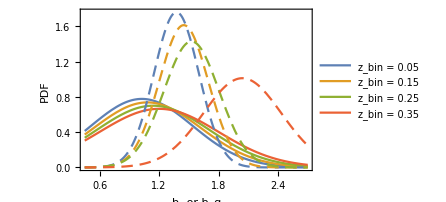

```mathematica
pbs=Plot[Evaluate[tabbs=Table[PDF[NormalDistribution[bsfidvec[[i]],σbs[[i]]],x],{i,1,zbinmax}]],{x,.45,2.7},Frame->True,FrameStyle->15,FrameLabel->{"b_s or b_g","PDF"},FrameTicks->{ Automatic,None},PlotRange->All,PlotLegends->Placed[{"z_bin = 0.05","z_bin = 0.15","z_bin = 0.25","z_bin = 0.35"},{Right,Top}]];
pbg=Plot[Evaluate[tabbg=Table[PDF[NormalDistribution[bgfidvec[[i]],σbg[[i]]],x],{i,1,zbinmax}]],{x,.45,2.7},Frame->True,FrameStyle->15,FrameLabel->{"bias","PDF"},PlotStyle->Dashing[{.025,.015}]];
sbsbg=Show[pbs,pbg,ImageSize->330]
```

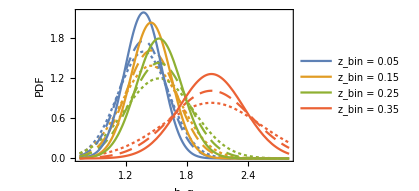

```mathematica
pbg6x2=Plot[Evaluate[tabbs=Table[PDF[NormalDistribution[bgfidvec[[i]],σbg[[i]]],x],{i,1,zbinmax}]],{x,.75,2.8},Frame->True,FrameStyle->14,FrameLabel->{"b_g","PDF"},FrameTicks->{ Automatic,None},PlotRange->All,PlotLegends->Placed[{"z_bin = 0.05","z_bin = 0.15","z_bin = 0.25","z_bin = 0.35"},{Right,Top}]];
pbg3x2=Plot[Evaluate[tabbg=Table[PDF[NormalDistribution[bgfidvec[[i]],σbg3x2[[i]]],x],{i,1,zbinmax}]],{x,.75,2.8},Frame->True,FrameStyle->14,FrameLabel->{"b_g","PDF"},FrameTicks->{ Automatic,None},PlotRange->All,PlotStyle->Dashing[{.03,.017}]];
pbg1x2=Plot[Evaluate[tabbg=Table[PDF[NormalDistribution[bgfidvec[[i]],σbg1x2[[i]]],x],{i,1,zbinmax}]],{x,.75,2.8},Frame->True,FrameStyle->14,FrameLabel->{"b_g","PDF"},FrameTicks->{ Automatic,None},PlotRange->All,PlotStyle->Dashing[{.007,.007}]];
sbsbg=Show[pbg1x2,pbg3x2,pbg6x2,ImageSize->310]
```

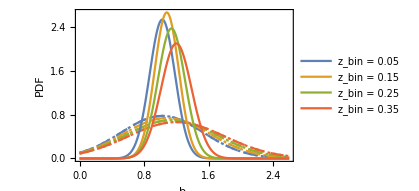

```mathematica
pbg6x2=Plot[Evaluate[tabbs=Table[PDF[NormalDistribution[bsfidvec[[i]],σbs[[i]]],x],{i,1,zbinmax}]],{x,0,2.6},Frame->True,FrameStyle->14,FrameLabel->{"b_s","PDF"},FrameTicks->{ Automatic,None},PlotRange->All,PlotLegends->Placed[{"z_bin = 0.05","z_bin = 0.15","z_bin = 0.25","z_bin = 0.35"},{Right,Top}]];
pbg3x2=Plot[Evaluate[tabbg=Table[PDF[NormalDistribution[bsfidvec[[i]],σbs3x2[[i]]],x],{i,1,zbinmax}]],{x,0,2.6},Frame->True,FrameStyle->14,FrameLabel->{"b_s","PDF"},FrameTicks->{ Automatic,None},PlotRange->All,PlotStyle->Dashing[{.03,.017}]];
pbg1x2=Plot[Evaluate[tabbg=Table[PDF[NormalDistribution[bsfidvec[[i]],σbs1x2[[i]]],x],{i,1,zbinmax}]],{x,0,2.6},Frame->True,FrameStyle->14,FrameLabel->{"b_s","PDF"},FrameTicks->{ Automatic,None},PlotRange->All,PlotStyle->Dashing[{.007,.007}]];
sbsbg=Show[pbg1x2,pbg3x2,pbg6x2,ImageSize->310]
```

```mathematica
pbs=Plot[Evaluate[tabbs=Table[PDF[NormalDistribution[bsfidvec[[i]],σbs[[i]]],x],{i,1,zbinmax}]],{x,.85,1.82},PlotRange->All,Frame->True,FrameStyle->15,FrameLabel->{"b_s","PDF"},FrameTicks->{ Automatic,None},PlotLegends->Placed[{"z_bin = 0.05","z_bin = 0.15","z_bin = 0.25","z_bin = 0.35","z_bin = 0.45","z_bin = 0.55","z_bin = 0.65"},{Right,Top}]]
pbg=Plot[Evaluate[tabbg=Table[PDF[NormalDistribution[bgfidvec[[i]],σbg[[i]]],x],{i,1,zbinmax}]],{x,.8,2.7},PlotRange->All,Frame->True,FrameStyle->15,FrameLabel->{"bias","PDF"},PlotStyle->Dashing[{.025,.015}]];
sbsbg=Show[pbs,ImageSize->330,PlotRange->All]
```

#### New Conservative Plots

```mathematica
(*cplotfun[σ8fid,iσ8,hh,ih,40]*)
```

```mathematica
(*cplotfun[Ωm0fid,iΩm0,σ8fid,iσ8,50]*)
```

```mathematica
cplotfun[σ8fid,iσ8,γfid,iγ,50]
```

```mathematica
cplotfun[Ωm0fid,iΩm0,Ωk0fid,iΩk0,30]
```

```mathematica
cplotfun[Ωm0fid,iΩm0,hh,ih,30]
```

```mathematica
cplotfun[hh,ih,Ωk0fid,iΩk0,30]
```

#### New Aggressive Plots

```mathematica
cplotfun[σ8fid,iσ8,γfid,iγ,80]
```

```mathematica
(*cplotfun[hh,ih,σ8fid,iσ8,60]*)
```

```mathematica
(*cplotfun[Ωm0fid,iΩm0,σ8fid,iσ8,50]*)
```

```mathematica
cplotfun[Ωk0fid,iΩk0,Ωm0fid,iΩm0,50]
```

```mathematica
cplotfun[Ωk0fid,iΩk0,hh,ih,50]
```

#### Final Plots

```mathematica
cplotfun[σ8fid,iσ8,γfid,iγ,100];
ggrid1={{"[◼]", "PlotGrid"}}[
{
{Show[plottab1[[1]],FrameTicks->{{Automatic,Automatic},{Thread[{tickstab1,tickstab2}],Automatic}}],plottab1[[2]],plottab1[[3]],plottab1[[4]],plottab1[[5]]}
},ImageSize->1300
];
```

```mathematica
Export["FM-comparison-AP-r10-phi0-b"<>ToString[bsstring]<>"-cons-kmax01-grid.png",ggrid1,ImageResolution->130]
```

FM-comparison-AP-r10-phi0-b1.0-cons-kmax01-grid.png

```mathematica
Show[sOm0Ok0cons,cmbplot3a,PlotRange->{{.245,.41},{-.11,.11}}]
```

```mathematica
sOk0hcons=cplotfun[hh,ih,Ωk0fid,iΩk0,30];
```

```mathematica
sOm0Ok0cons=cplotfun[Ωm0fid,iΩm0,Ωk0fid,iΩk0,90];
sOm0hcons=cplotfun[Ωm0fid,iΩm0,hh,ih,90];
```

```mathematica
ggridOm0Ok0={{"[◼]", "PlotGrid"}}[
{
{sOm0Ok0cons,sOm0Ok0aggr}
},ImageSize->640
];
```

```mathematica
sOm0Ok0aggr=cplotfun[Ωm0fid,iΩm0,Ωk0fid,iΩk0,90];
sOm0haggr=cplotfun[Ωm0fid,iΩm0,hh,ih,90];
```

```mathematica
ggridOm0h={{"[◼]", "PlotGrid"}}[
{
{sOm0hcons,sOm0haggr}
},ImageSize->640
];
```

```mathematica
(*Export["FM-comparison-Om0Ok0-r10-phi0-b1.0-cons-aggr-kmax01-grid.png",ggridOm0Ok0,ImageResolution->130]
Export["FM-comparison-Om0Oh-r10-phi0-b1.0-cons-aggr-kmax01-grid.png",ggridOm0h,ImageResolution->130]*)
```

```mathematica
cplotfun[σ8fid,iσ8,γfid,iγ,120];
ggrid1={{"[◼]", "PlotGrid"}}[
{
{plottab1[[1]],plottab1[[2]],plottab1[[3]],plottab1[[4]]},
{plottab1[[5]],plottab1[[6]],plottab1[[7]],plottab1[[8]]}
},ImageSize->1100
];
```

```mathematica
(*Export["FM-comparison-AP-r10-phi0-b"<>ToString[bsstring]<>"-aggr-kmax01-grid.png",ggrid1,ImageResolution->130]*)
```

## LSST 6×2pt FM; no AP: σ_8, γ, h, Ω_m0& Ω_k0

```mathematica
bschoice=1.0;
```

```mathematica
bschoice=1.5;
```

### Preamble

```mathematica
Clear[CC2,CC3,Υ,Pmmfun]
Ωk0fid=0;
F2[z_]:=((1+z)^2-1)/(2 EE[z]^2);F3[z_]:=((1+z)^3-1)/(2 EE[z]^2);
CC2full[z_]:=((-1)/dCoverdH[z])NIntegrate[F2[zz]/EE[zz],{zz,0,z}]+(1/6)dCoverdH[z]^2;
CC3full[z_]:=((-1)/dCoverdH[z])NIntegrate[F3[zz]/EE[zz],{zz,0,z}];
(* pre-computing these factors *)
AbsoluteTiming[CC2=Interpolation[Map[{#,CC2full[#]}&,zzvec]]]
AbsoluteTiming[CC3=Interpolation[Map[{#,CC3full[#]}&,zzvec]]]
```

{0.0322152,InterpolatingFunction[…]}

{0.0325327,InterpolatingFunction[…]}

```mathematica
σδfid=4.24;σgfid=4.24;σvfid=6√2;r=10;
FMfun[case_]:=Module[{},
ngg[z_]:=r 10^-0 nsnfun[z];nggvec=Map[ngg,zzvec];
nδδ[z_]:=10^-0 nsnfun[z];nδδvec=Map[nδδ,zzvec];
nvv[z_]:=10^-0 nsnfun[z];nvvvec=Map[nvv,zzvec];
ngδ[z_]:=(0/1)Min[ngg[z],nδδ[z]] ;(* zero/half/all of the SN are in observed galaxies *)


Clear[Hr,Sδ,Sv,nPδδ,nPδv,nPvv,Cab,CabInv];
bsfid[z_]:=bschoice/G[z];    (* 1.5/G[z] or 1.0/G[z] *)
bgfid[z_]:=Piecewise[{{1.34/G[z],z<=0.3},{1.7/G[z],z>0.3}}];
bsfidvec=Map[bsfid,zzvec];
bgfidvec=Map[bgfid,zzvec];

(*Gvec=Map[G,zzvec];*)
(* fid Pmm(k) in (h/Mpc)^3*)
(*Pmmfun[k_,z_,σ8_,γ_]:=Gγ[z,γ]^2 (σ8/σ8camb)^2 powerinterp[k];*) 

(* Trick to compute derivative wrt to Ωm0, Ωk0 and h analytically *)
(*Pmmfun[k_,z_,σ8_,γ_,Ωm0_]:=Gγ[z,γ]^2 (σ8/σ8camb)^2 powerinterp[k]+(Ωm0-Ωm0fid)Gγ[z,γ]^2 (σ8/σ8camb)^2 dpdΩm0fun[k]; *)
Υ[Ωm0_,Ωk0_,h_,z_]:=1;
Pmmfun[k_,z_,σ8_,γ_,Ωm0_,Ωk0_,h_,μ_]:=Υ[Ωm0,Ωk0,h,z] Gγ[z,γ]^2 (σ8/σ8camb)^2 (powerinterp[k]+(Ωm0-Ωm0fid)(dpdΩm0fun[k])+(Ωk0-Ωk0fid)(dpdΩk0fun[k])+(h-hh)(dpdhfun[k]+0dPmmdlnk[k]/hh));
(*Pmmfun[k_,z_,σ8_,γ_,Ωm0_,Ωk0_,μ_]:=Gγ[z,γ]^2 (σ8/σ8camb)^2 powerinterp[k]+(Ωm0-Ωm0fid)Gγ[z,γ]^2 (σ8/σ8camb)^2 dpdΩm0fun[k];*)


(*Hr[z_,Ωm0_]:=2998^-1 EEΩm0[z,Ωm0]; *)(* in h/Mpc *)
Hr[z_,Ωm0_,Ωk0_,h_]:=2998^-1 EEΩm0Ωk0[z,Ωm0,Ωk0](h/hh); (* in h/Mpc *)

σvnonlinsq=(300/299792)^2;
σveffsq[z_,σint_]:=((Log[10]/5)σint)^2(dCoverdH[z] /(dCoverdH[z] - (1+z)/EE[z]))^2+σvnonlinsq;
(*Sδ[k_,μ_,σδ_]:=1;Sv[k_,σv_]:=1;*)

Sδ[k_,μ_,σδ_]:=Exp[-(1/4)(k μ σδ)^2]; Sv[k_,μ_,σv_]:=Exp[-(1/4)(k μ σv)^2];Sg[k_,μ_,σg_]:=Exp[-(1/4)(k μ σg)^2];

(* I now use 2 μ variables: μ and μr. This is to avoid differentiating μr by mistake. Afterall, the deriv. wrt to ln k, already performed before, result in terms which depend on μr *)
nPδδ[k_,μ_,μr_,z_,σ8_,γ_,bs_,σv_,σδ_,Ωm0_,Ωk0_,h_]:=nδδ[z]((1+(ffγ[z,γ]/bs)μ^2)^2 bs^2 Sδ[k,μ,σδ]^2 Pmmfun[k,z,σ8,γ,Ωm0,Ωk0,h,μr]+1/nδδ[z]);
nPgg[k_,μ_,μr_,z_,σ8_,γ_,bg_,σv_,σg_,Ωm0_,Ωk0_,h_]:=nδδ[z]((1+(ffγ[z,γ]/bg)μ^2)^2 bg^2 Sg[k,μ,σg]^2 Pmmfun[k,z,σ8,γ,Ωm0,Ωk0,h,μr]+1/ngg[z]);
nPδv[k_,μ_,μr_,z_,σ8_,γ_,bs_,σv_,σδ_,Ωm0_,Ωk0_,h_]:=nδδ[z](1+(ffγ[z,γ]/bs)μ^2)((Hr[z,Ωm0,Ωk0,h] μ Sv[k,μ,σv])/(k(1+z)))ffγ[z,γ] bs Sδ[k,μ,σδ]Pmmfun[k,z,σ8,γ,Ωm0,Ωk0,h,μr];
nPgv[k_,μ_,μr_,z_,σ8_,γ_,bg_,σv_,σg_,Ωm0_,Ωk0_,h_]:=nδδ[z](1+(ffγ[z,γ]/bg)μ^2)((Hr[z,Ωm0,Ωk0,h] μ Sv[k,μ,σv])/(k(1+z)))ffγ[z,γ] bg Sg[k,μ,σg]Pmmfun[k,z,σ8,γ,Ωm0,Ωk0,h,μr];
nPδg[k_,μ_,μr_,z_,σ8_,γ_,bs_,bg_,σv_,σδ_,σg_,Ωm0_,Ωk0_,h_]:=nδδ[z]((1+(ffγ[z,γ]/bs)μ^2)(1+(ffγ[z,γ]/bg)μ^2)bs bg Sδ[k,μ,σδ]Sg[k,μ,σg]Pmmfun[k,z,σ8,γ,Ωm0,Ωk0,h,μr]+ngδ[z]/(ngg[z]nδδ[z]));
nPvv[k_,μ_,μr_,z_,σ8_,γ_,σv_,σδ_,σint_,Ωm0_,Ωk0_,h_]:=nδδ[z](((Hr[z,Ωm0,Ωk0,h] μ Sv[k,μ,σv])/(k(1+z)))^2 ffγ[z,γ]^2 Pmmfun[k,z,σ8,γ,Ωm0,Ωk0,h,μr]+σveffsq[z,σint]/nvv[z]);

Which[case==0,(* vv *)
{Cab[k_,μ_,μr_,σ8_,γ_,bs_,bg_,σv_,σδ_,σg_,z_,σint_,Ωm0_,Ωk0_,h_]:={{nPvv[k,μ,μr,z,σ8,γ,σv,σδ,σint,Ωm0,Ωk0, h]}};
CabInv[k_,μ_,μr_,σ8_,γ_,bs_,bg_,σv_,σδ_,σg_,z_,σint_,Ωm0_,Ωk0_,h_]:=Inverse[Cab[k,μ,μr,σ8,γ,bs,bg,σv,σδ,σg,z,σint,Ωm0,Ωk0, h]];},
case==1,(* gg *)
{Cab[k_,μ_,μr_,σ8_,γ_,bs_,bg_,σv_,σδ_,σg_,z_,σint_,Ωm0_,Ωk0_,h_]:={{nPgg[k,μ,μr,z,σ8,γ,bg,σv,σg,Ωm0,Ωk0, h]}};
CabInv[k_,μ_,μr_,σ8_,γ_,bs_,bg_,σv_,σδ_,σg_,z_,σint_,Ωm0_,Ωk0_,h_]:=Inverse[Cab[k,μ,μr,σ8,γ,bs,bg,σv,σδ,σg,z,σint,Ωm0,Ωk0, h]];},
case==2,(* 3×2 g-s *)
{Cab[k_,μ_,μr_,σ8_,γ_,bs_,bg_,σv_,σδ_,σg_,z_,σint_,Ωm0_,Ωk0_,h_]:={{nPvv[k,μ,μr,z,σ8,γ,σv,σδ,σint,Ωm0,Ωk0, h],nPgv[k,μ,μr,z,σ8,γ,bg,σv,σg,Ωm0,Ωk0, h]},{nPgv[k,μ,μr,z,σ8,γ,bg,σv,σg,Ωm0,Ωk0, h],nPgg[k,μ,μr,z,σ8,γ,bg,σv,σg,Ωm0,Ωk0, h]}};
CabInv[k_,μ_,μr_,σ8_,γ_,bs_,bg_,σv_,σδ_,σg_,z_,σint_,Ωm0_,Ωk0_,h_]:=Inverse[Cab[k,μ,μr,σ8,γ,bs,bg,σv,σδ,σg,z,σint,Ωm0,Ωk0, h]];},
case==3,(* 6×2 *)
{Cab[k_,μ_,μr_,σ8_,γ_,bs_,bg_,σv_,σδ_,σg_,z_,σint_,Ωm0_,Ωk0_,h_]:={{nPδδ[k,μ,μr,z,σ8,γ,bs,σv,σδ,Ωm0,Ωk0, h],nPδv[k,μ,μr,z,σ8,γ,bs,σv,σδ,Ωm0,Ωk0, h],nPδg[k,μ,μr,z,σ8,γ,bs,bg,σv,σδ,σg,Ωm0,Ωk0, h]},{nPδv[k,μ,μr,z,σ8,γ,bs,σv,σδ,Ωm0,Ωk0, h],nPvv[k,μ,μr,z,σ8,γ,σv,σδ,σint,Ωm0,Ωk0, h],nPgv[k,μ,μr,z,σ8,γ,bg,σv,σg,Ωm0,Ωk0, h]},{nPδg[k,μ,μr,z,σ8,γ,bs,bg,σv,σδ,σg,Ωm0,Ωk0, h],nPgv[k,μ,μr,z,σ8,γ,bg,σv,σg,Ωm0,Ωk0, h],nPgg[k,μ,μr,z,σ8,γ,bg,σv,σg,Ωm0,Ωk0, h]}};
CabInv[k_,μ_,μr_,σ8_,γ_,bs_,bg_,σv_,σδ_,σg_,z_,σint_,Ωm0_,Ωk0_,h_]:=Inverse[Cab[k,μ,μr,σ8,γ,bs,bg,σv,σδ,σg,z,σint,Ωm0,Ωk0, h]];}
];

Print[Cab[.1,.5,.5,.83,γfid,bsfid[.1],bgfid[.1],σvfid,σδfid,σgfid,.15,.13,Ωm0fid,Ωk0fid,hh]];
Print[CabInv[.1,.5,.5,.83,γfid,bsfid[.1],bgfid[.1],σvfid,σδfid,σgfid,.15,.13,Ωm0fid,Ωk0fid,hh]];
Print[Map[Det[Cab[.1,.5,.5,.83,γfid,bsfid[.1],bgfid[#],σvfid,σδfid,σgfid,#,.13,Ωm0fid,Ωk0fid,hh]]&,zzvec]];

Clear[kr,Fbar,FMtot,FM,zz,z,FMvec];

Fbar[p1_,p2_,z_,σint_]:=multfact(1/2)du Total[Map[Tr[(D[Cab[kr,μ[Ωm0,Ωk0],#,σ8,γ,bs,bg,σv,σδ,σg,z,σint,Ωm0,Ωk0, h],p1]/.{μ[Ωm0,Ωk0]->#,Derivative[1,0][μ][Ωm0,Ωk0]->#(1-#^2)(F3[z]+CC3[z]), Derivative[0,1][μ][Ωm0,Ωk0]->#(1-#^2)(F2[z]+CC2[z])}/.{σ8->σ8fid,γ->γfid,bs->bsfid[z],bg->bgfid[z],σv->σvfid,σδ->σδfid,σg->σgfid, Ωm0->Ωm0fid, Ωk0->Ωk0fid, h-> hh}).CabInv[kr,#,#,σ8fid,γfid,bsfid[z],bgfid[z],σvfid,σδfid,σgfid,z,σint,Ωm0fid,Ωk0fid, hh].(D[Cab[kr,μ[Ωm0,Ωk0],#,σ8,γ,bs,bg,σv,σδ,σg,z,σint,Ωm0,Ωk0, h],p2]/.{μ[Ωm0,Ωk0]->#,Derivative[1,0][μ][Ωm0,Ωk0]->#(1-#^2)(F3[z]+CC3[z]), Derivative[0,1][μ][Ωm0,Ωk0]->#(1-#^2)(F2[z]+CC2[z])}/.{σ8->σ8fid,γ->γfid,bs->bsfid[z],bg->bgfid[z],σv->σvfid,σδ->σδfid,σg->σgfid, Ωm0->Ωm0fid, Ωk0->Ωk0fid, h-> hh}).CabInv[kr,#,#,σ8fid,γfid,bsfid[z],bgfid[z],σvfid,σδfid,σgfid,z,σint,Ωm0fid,Ωk0fid, hh]]&,μvec]];


kmax=0.1;
Δkfact=1;
du=1/10;
{μvec=Range[du/2,1-du/2,du]; multfact=2;};

(*{μvec=Range[-1+du/2,1-du/2,du]; multfact=1;};*)

{iσ8,iγ,iσv,iσδ,iσg,iΩm0,iΩk0,ih}=2zbins+{1,2,3,4,5,6,7,8};
AbsoluteTiming[Monitor[FMvec=
ParallelTable[
zz=zzvec[[iz]];
kmin=kminvecΔz0p1[[iz,2]];Δk=Δkfact 2π/ΔVvec[[iz]]^(1/3);
(* k starts at kmax and go down until kmin *)
kbins=Range[kmax,kmin,-Δk];kbins=Join[kbins,{kmin}];
Δklast=kbins[[-2]]-kmin; (* the last kbin is smaller in order not to go below kmin *)
kvec=MovingAverage[kbins,2]; (* central ks *)
FMlength=2zbins+8;
FMtot=Table[0,{i,FMlength},{j,FMlength}];
Do[
FM=Table[0,{i,FMlength},{j,FMlength}];
kr=kvec[[ik]];
If[ik==Length[kvec],VVk=(Δklast/Δk)((Δkfact kr^2 ΔVvec[[iz]]^(2/3))/(2π)),VVk=(Δkfact kr^2 ΔVvec[[iz]]^(2/3))/(2π)];

FM[[2iz-1,2iz-1]]=Fbar[bs,bs,zz,σintfid];
FM[[2iz-1,2iz]]=Fbar[bs,bg,zz,σintfid];
FM[[2iz-1,iσ8]]=Fbar[bs,σ8,zz,σintfid];
FM[[2iz-1,iγ]]=Fbar[bs,γ,zz,σintfid];
FM[[2iz-1,iσv]]=Fbar[bs,σv,zz,σintfid];
FM[[2iz-1,iσδ]]=Fbar[bs,σδ,zz,σintfid];
FM[[2iz-1,iσg]]=Fbar[bs,σg,zz,σintfid];
FM[[2iz-1,iΩm0]]=Fbar[bs,Ωm0,zz,σintfid];
FM[[2iz-1,iΩk0]]=Fbar[bs,Ωk0,zz,σintfid];
FM[[2iz-1,ih]]=Fbar[bs,h,zz,σintfid];

FM[[2iz,2iz]]=Fbar[bg,bg,zz,σintfid];
FM[[2iz,iσ8]]=Fbar[bg,σ8,zz,σintfid];
FM[[2iz,iγ]]=Fbar[bg,γ,zz,σintfid];
FM[[2iz,iσv]]=Fbar[bg,σv,zz,σintfid];
FM[[2iz,iσδ]]=Fbar[bg,σδ,zz,σintfid];
FM[[2iz,iσg]]=Fbar[bg,σg,zz,σintfid];
FM[[2iz,iΩm0]]=Fbar[bg,Ωm0,zz,σintfid];
FM[[2iz,iΩk0]]=Fbar[bg,Ωk0,zz,σintfid];
FM[[2iz,ih]]=Fbar[bg,h,zz,σintfid];

FM[[iσ8,iσ8]]=Fbar[σ8,σ8,zz,σintfid];
FM[[iσ8,iγ]]=Fbar[σ8,γ,zz,σintfid];
FM[[iσ8,iσv]]=Fbar[σ8,σv,zz,σintfid];
FM[[iσ8,iσδ]]=Fbar[σ8,σδ,zz,σintfid];
FM[[iσ8,iσg]]=Fbar[σ8,σg,zz,σintfid];
FM[[iσ8,iΩm0]]=Fbar[σ8,Ωm0,zz,σintfid];
FM[[iσ8,iΩk0]]=Fbar[σ8,Ωk0,zz,σintfid];
FM[[iσ8,ih]]=Fbar[σ8,h,zz,σintfid];

FM[[iγ,iγ]]=Fbar[γ,γ,zz,σintfid];
FM[[iγ,iσv]]=Fbar[γ,σv,zz,σintfid];
FM[[iγ,iσδ]]=Fbar[γ,σδ,zz,σintfid];
FM[[iγ,iσg]]=Fbar[γ,σg,zz,σintfid];
FM[[iγ,iΩm0]]=Fbar[γ,Ωm0,zz,σintfid];
FM[[iγ,iΩk0]]=Fbar[γ,Ωk0,zz,σintfid];
FM[[iγ,ih]]=Fbar[γ,h,zz,σintfid];

FM[[iσv,iσv]]=Fbar[σv,σv,zz,σintfid];
FM[[iσv,iσδ]]=Fbar[σv,σδ,zz,σintfid];
FM[[iσv,iσg]]=Fbar[σv,σg,zz,σintfid];
FM[[iσv,iΩm0]]=Fbar[σv,Ωm0,zz,σintfid];
FM[[iσv,iΩk0]]=Fbar[σv,Ωk0,zz,σintfid];
FM[[iσv,ih]]=Fbar[σv,h,zz,σintfid];
FM[[iσδ,iσδ]]=Fbar[σδ,σδ,zz,σintfid];
FM[[iσδ,iσg]]=Fbar[σδ,σg,zz,σintfid];
FM[[iσδ,iΩm0]]=Fbar[σδ,Ωm0,zz,σintfid];
FM[[iσδ,iΩk0]]=Fbar[σδ,Ωk0,zz,σintfid];
FM[[iσδ,ih]]=Fbar[σδ,h,zz,σintfid];
FM[[iσg,iσg]]=Fbar[σg,σg,zz,σintfid];
FM[[iσg,iΩm0]]=Fbar[σg,Ωm0,zz,σintfid];
FM[[iσg,iΩk0]]=Fbar[σg,Ωk0,zz,σintfid];
FM[[iσg,ih]]=Fbar[σg,h,zz,σintfid];
FM[[iΩm0,iΩm0]]=Fbar[Ωm0,Ωm0,zz,σintfid];
FM[[iΩm0,iΩk0]]=Fbar[Ωm0,Ωk0,zz,σintfid];
FM[[iΩm0,ih]]=Fbar[Ωm0,h,zz,σintfid];
FM[[iΩk0,iΩk0]]=Fbar[Ωk0,Ωk0,zz,σintfid];
FM[[iΩk0,ih]]=Fbar[Ωk0,h,zz,σintfid];
FM[[ih,ih]]=Fbar[h,h,zz,σintfid];

(* symmetrizes the FM assuming empty elements are zero *)
FM=FM+Transpose[FM]-DiagonalMatrix[Diagonal[FM]]; 

FMtot+=VVk FM;
,{ik,Length[kvec]}];
FMtot
,{iz,1,zbins}];,{iz,ik,Length[kvec]}]];
Print[FMvec[[1]]//MatrixForm];
]
```

```mathematica
(* 50% error bar in the priors *)
(*relσb=.5;relσσ=.5;
FMprior=DiagonalMatrix[{(bsfidvec[[1]] relσb)^-2,(bgfidvec[[1]]relσb)^-2,(bsfidvec[[2]] relσb)^-2,(bgfidvec[[2]]relσb)^-2,(bsfidvec[[3]] relσb)^-2,(bgfidvec[[3]]relσb)^-2,(bsfidvec[[4]] relσb)^-2,(bgfidvec[[4]]relσb)^-2,(bsfidvec[[5]] relσb)^-2,(bgfidvec[[5]]relσb)^-2,(σ8fid 1000)^-2,(γfid 1000)^-2,(σvfid relσσ)^-2,(σδfid relσσ)^-2,(σδfid relσσ)^-2}];
Print[Dimensions[FMprior]];
Print[Diagonal[FMprior]];*)
```

## Constant bias in each bin: b(z)

### FM for σ_8 × γ, b(z), P_δδ, P_δv, P_vv

Parameter order:
 bs1,bg1,..., bsn,bgn, σ8, γ, σv, σδ, σg

```mathematica
CloseKernels[];
```

```mathematica
{bschoice,forecast,r}
bsfid[z_]:=bschoice/G[z];    (* 1.5/G[z] or 1.0/G[z] *)
bgfid[z_]:=Piecewise[{{1.34/G[z],z<=0.3},{1.7/G[z],z>0.3}}];
bsfidvec=Map[bsfid,zzvec];
bgfidvec=Map[bgfid,zzvec];
bsstring=ToString[DecimalForm[bschoice,{2,1}]];
rstring=ToString[r];
If[forecast==0,{forecaststr="-cons",zbins=4},{forecaststr="-aggr",zbins=7}];
forecast
CloseKernels[];
LaunchKernels[zbins];
relσb=.5;relσσ=.5;relσh=.5;
FMprior=DiagonalMatrix[
Flatten[Join[Table[{(bsfidvec[[iz]] relσb)^-2,(bgfidvec[[iz]]relσb)^-2},{iz,1,zbins}],{(σ8fid 1000)^-2,(γfid 1000)^-2,(σvfid relσσ)^-2,(σδfid relσσ)^-2,(σδfid relσσ)^-2,(Ωm0fid 1000)^-2,(.5)^-2,(hh relσh)^-2}]]
];
Print[Dimensions[FMprior]];
Print[Diagonal[FMprior]];
```

{1.,0,10}

0

{16,16}

{3.79714,2.11469,3.41984,1.90456,3.08026,1.71545,2.7769,0.960867,1.45159×10^-6,3.36672×10^-6,0.0555556,0.222499,0.222499,0.0000111111,4.,8.16327}

### FM Plots b(z)

```mathematica
{zbinmin,zbinmax}={1,4};
bschoice=1.0;
bsstring=ToString[DecimalForm[bschoice,{2,1}]];{iσ8,iγ,iσv,iσδ,iσg,iΩm0,iΩk0,ih}=2zbinmax+{1,2,3,4,5,6,7,8};
FM6x2 =ToExpression[Import[FMdir<>"FM-6x2-noAP-r10-phi0-b"<>ToString[bsstring]<>"-cons-kmax01-zmax04.tab","List"]];
FM3x2 =ToExpression[Import[FMdir<>"FM-3x2gs-noAP-r10-phi0-b"<>ToString[bsstring]<>"-cons-kmax01-zmax04.tab","List"]];
FMgg=ToExpression[Import[FMdir<>"FM-Pgg-noAP-r10-phi0-b"<>ToString[bsstring]<>"-cons-kmax01-zmax04.tab","List"]];
FMvv =ToExpression[Import[FMdir<>"FM-Pvv-noAP-phi0-b"<>ToString[bsstring]<>"-cons-kmax01-zmax04.tab","List"]];
bsfid[z_]:=bschoice/G[z];    (* 1.5/G[z] or 1.0/G[z] *)
bgfid[z_]:=Piecewise[{{1.34/G[z],z<=0.3},{1.7/G[z],z>0.3}}];
bsfidvec=Map[bsfid,zzvec];bgfidvec=Map[bgfid,zzvec];
relσb=.5;relσσ=.5;σΩm0prior=.5;relσh=.7;
FMprior=DiagonalMatrix[
Flatten[Join[Table[{(bsfidvec[[iz]] relσb)^-2,(bgfidvec[[iz]]relσb)^-2},{iz,1,zbinmax}],{(σ8fid 1000)^-2,(γfid 1000)^-2,(σvfid relσσ)^-2,(σδfid relσσ)^-2,(σδfid relσσ)^-2,(σΩm0prior)^-2,(σΩm0prior)^-2,(hh relσh)^-2}]]
];
Dimensions[FMprior]
Dimensions[FM3x2]
Round[FoM1=Det[ Inverse[Inverse[Total[FMgg,{1}]+FMprior][[iσ8;;iγ,iσ8;;iγ]]]]^(1/2),1]
Round[FoM2=Det[Inverse[Inverse[Total[FM3x2,{1}]+FMprior][[iσ8;;iγ,iσ8;;iγ]]]]^(1/2),1]
Round[FoM3=Det[Inverse[Inverse[Total[FM6x2,{1}]+FMprior][[iσ8;;iγ,iσ8;;iγ]]]]^(1/2),1]
Round[{FoM3/FoM2,FoM3/FoM1},.01]
```

{16,16}

{4,16,16}

39

62

83

{1.34,2.13}

```mathematica
{zbinmin,zbinmax}={1,4};
bschoice=1.0;
bsstring=ToString[DecimalForm[bschoice,{2,1}]];{iσ8,iγ,iσv,iσδ,iσg,iΩm0,iΩk0,ih}=2zbinmax+{1,2,3,4,5,6,7,8};
FM6x2 =ToExpression[Import[FMdir<>"FM-6x2-noAPh-r10-phi0-b"<>ToString[bsstring]<>"-cons-kmax01-zmax04.tab","List"]];
FM3x2 =ToExpression[Import[FMdir<>"FM-3x2gs-noAPh-r10-phi0-b"<>ToString[bsstring]<>"-cons-kmax01-zmax04.tab","List"]];
FMgg=ToExpression[Import[FMdir<>"FM-Pgg-noAPh-r10-phi0-b"<>ToString[bsstring]<>"-cons-kmax01-zmax04.tab","List"]];
FMvv =ToExpression[Import[FMdir<>"FM-Pvv-noAPh-phi0-b"<>ToString[bsstring]<>"-cons-kmax01-zmax04.tab","List"]];
bsfid[z_]:=bschoice/G[z];    (* 1.5/G[z] or 1.0/G[z] *)
bgfid[z_]:=Piecewise[{{1.34/G[z],z<=0.3},{1.7/G[z],z>0.3}}];
bsfidvec=Map[bsfid,zzvec];bgfidvec=Map[bgfid,zzvec];
relσb=.5;relσσ=.5;σΩm0prior=.5;relσh=.7;
FMprior=DiagonalMatrix[
Flatten[Join[Table[{(bsfidvec[[iz]] relσb)^-2,(bgfidvec[[iz]]relσb)^-2},{iz,1,zbinmax}],{(σ8fid 1000)^-2,(γfid 1000)^-2,(σvfid relσσ)^-2,(σδfid relσσ)^-2,(σδfid relσσ)^-2,(σΩm0prior)^-2,(σΩm0prior)^-2,(hh relσh)^-2}]]
];
Dimensions[FMprior]
Dimensions[FM3x2]
Round[FoM1=Det[ Inverse[Inverse[Total[FMgg,{1}]+FMprior][[iσ8;;iγ,iσ8;;iγ]]]]^(1/2),1]
Round[FoM2=Det[Inverse[Inverse[Total[FM3x2,{1}]+FMprior][[iσ8;;iγ,iσ8;;iγ]]]]^(1/2),1]
Round[FoM3=Det[Inverse[Inverse[Total[FM6x2,{1}]+FMprior][[iσ8;;iγ,iσ8;;iγ]]]]^(1/2),1]
Round[{FoM3/FoM2,FoM3/FoM1},.01]
```

{16,16}

{4,16,16}

42

60

87

{1.45,2.05}

```mathematica
{iσ8,iγ,iσv,iσδ,iσg,iΩm0,iΩk0,ih}=2zbinmax+{1,2,3,4,5,6,7,8};
pstringvec=Join[Table["",{2zbinmax}],{"σ_8","γ","σv","σδ","σg","Ω_m0","Ω_k0","h"}];
pminmax=Join[Table[{0,1},{2zbinmax}],{{.18,1.48},{-.6,1.7},{0,1},{0,1},{0,1},{.24,.36},{-1.3,1.3},{.52,.88}}];
pminmax=Join[Table[{0,1},{2zbinmax}],{{0,1.68},{-.9,2.0},{0,1},{0,1},{0,1},{.24,.36},{-1.3,1.3},{.52,.88}}];
cplotfun[p1fid_,ip1_,p2fid_,ip2_,npoints_]:=Module[{},
pstring={pstringvec[[ip1]],pstringvec[[ip2]]};
(*Print[zbinmax];*)
(*Print[Round[Diagonal[Inverse[Total[FM6x2,{1}]]]^(1/2),.001]];*)
tickstab1=Table[.1ix,{ix,1,18}];
tickstab2=Table[If[Mod[ix,4]==2,DecimalForm[.1ix,{2,1}],""],{ix,1,18}];
tickstab1Om0=Table[.01ix,{ix,1,40}];
tickstab2Om0=Table[If[Mod[ix,4]==2,DecimalForm[.01ix,{2,2}],""],{ix,1,40}];

If[{ip1,ip2}=={iσ8,iγ},myticks=Thread[{tickstab1,tickstab2}],myticks=Automatic];
(*If[ip1==iΩm0,myticks=Thread[{tickstab1Om0,tickstab2Om0}],myticks=Automatic];*)
plottab1=Table[
If[iz==zbinmax+1,{z1,z2}={1,zbinmax},{z1,z2}={iz,iz}];

{p1min,p1max}=pminmax[[ip1]];
{p2min,p2max}=pminmax[[ip2]];

p1list=Range[p1min,p1max,(p1max-p1min)/npoints];
p2list=Range[p2min,p2max,(p2max-p2min)/npoints];

prange={{p1min,p1max},{p2min,p2max}};

chisqvv=FMmargchisqfun[FMvv,z1,z2,ip1,p1fid,p1list,ip2,p2fid,p2list];
chisq3x2=FMmargchisqfun[FM3x2,z1,z2,ip1,p1fid,p1list,ip2,p2fid,p2list];
chisqdd=FMmargchisqfun[FMgg,z1,z2,ip1,p1fid,p1list,ip2,p2fid,p2list];
chisq6x2=FMmargchisqfun[FM6x2,z1,z2,ip1,p1fid,p1list,ip2,p2fid,p2list];

lpdd=lplotddfun[chisqdd,{2.3,6.17,11.8},pstring];
lpvv=lplotvvfun[chisqvv,{2.3,6.17,11.8},pstring];
lp3x2=lplotfullfun[chisq3x2,{2.3,6.17,11.8},pstring];
lp6x2=lplot6x2fun[chisq6x2,{2.3,6.17,11.8},pstring];

(*pos1={.74p1max-.32,.07};{row={0,-.27},pos2=pos1+row,pos3=pos2+row,pos4=pos3+row,pos5=pos4+row};
Δpos={.39+.03,.06};square={.06,.11};style=20;*)
pos1={.55,.34};{row={0,-.075},pos2=pos1+row,pos3=pos2+row,pos4=pos3+row,pos5=pos4+row};
Δpos={.23,.02};square={.033,.033};style=19;

rect[pos_]:=Rectangle[Scaled[pos],Scaled[pos+square]];
If[iz==1,s3=Show[lpvv,lpdd,lp3x2,lp6x2,Graphics[Text[Style["z_bin="<>ToString[zzvec[[iz]]],21],{p1min+.2p1max,.88p2max}]],PlotRange->prange],
If[iz==zbinmax+1,
If[{ip1,ip2}=={iσ8,iγ},
s3=Show[lpvv,lpdd,lp3x2,lp6x2,cmbplot,Graphics[Text[Style["z ∈ [0, "<>ToString[zbinmax/10.]<>"]",21],Scaled[{.25,.91}]]],Graphics[{color6x2,rect[pos1],colorfull,rect[pos2],colordd,rect[pos3],Darker[colorvv,.3],rect[pos4],mantzblue,rect[pos5],
Black,Text[Style["6x2 g-s-s",style],Scaled[pos1+Δpos]],Text[Style["3x2 g-s    ",style],Scaled[pos2+Δpos]],Text[Style["1x2 gals δ ",style],Scaled[pos3+Δpos+{.01,0}]],Text[Style["1x2 SN v  ",style],Scaled[pos4+Δpos]],Text[Style["CMB        ",style],Scaled[pos5+Δpos]]}],
PlotRange->prange,FrameTicks->{{Automatic,Automatic},{Thread[{tickstab1,tickstab2}],Automatic}}],s3=Show[lpvv,lpdd,lp3x2,lp6x2,Graphics[Text[Style["z ∈ [0, "<>ToString[zbinmax/10.]<>"]",21],Scaled[{.25,.91}](*{p1min+.24p1max,.88p2max}*)]],Graphics[{color6x2,rect[pos2],colorfull,rect[pos3],colordd,rect[pos4],Darker[colorvv,.3],rect[pos5],
Black,Text[Style["6x2 g-s-s",style],Scaled[pos2+Δpos]],Text[Style["3x2 g-s    ",style],Scaled[pos3+Δpos]],Text[Style["1x2 gals δ ",style],Scaled[pos4+Δpos+{.01,0}]],Text[Style["1x2 SN v  ",style],Scaled[pos5+Δpos]]}],
PlotRange->prange,FrameTicks->{{Automatic,Automatic},{myticks,Automatic}}]],
s3=Show[lpvv,lpdd,lp3x2,lp6x2,Graphics[Text[Style["z_bin="<>ToString[zzvec[[iz]]],21],{p1min+.2p1max,.88p2max}]],PlotRange->prange,FrameTicks->{{Automatic,Automatic},{myticks,Automatic}}(*,PlotLabel-> "b(z), marg. all, kmax=0.1",LabelStyle->15*)]]],
{iz,1,zbinmax+1}];
s3
]
```

#### Final Plots

```mathematica
cplotfun[σ8fid,iσ8,γfid,iγ,100];
ggrid1={{"[◼]", "PlotGrid"}}[
{
{Show[plottab1[[1]],FrameTicks->{{Automatic,Automatic},{Thread[{tickstab1,tickstab2}],Automatic}}],plottab1[[2]],plottab1[[3]],plottab1[[4]],plottab1[[5]]}
},ImageSize->1300
];
```

```mathematica
Export["FM-comparison-AP-r10-phi0-b"<>ToString[bsstring]<>"-cons-kmax01-grid.png",ggrid1,ImageResolution->130]
```

FM-comparison-AP-r10-phi0-b1.0-cons-kmax01-grid.png

```mathematica
sOm0Ok0cons=cplotfun[Ωm0fid,iΩm0,Ωk0fid,iΩk0,90];
sOm0hcons=cplotfun[Ωm0fid,iΩm0,hh,ih,90];
```

```mathematica
ggridOm0Ok0={{"[◼]", "PlotGrid"}}[
{
{sOm0Ok0cons,sOm0Ok0aggr}
},ImageSize->640
];
```

```mathematica
sOm0Ok0aggr=cplotfun[Ωm0fid,iΩm0,Ωk0fid,iΩk0,90];
sOm0haggr=cplotfun[Ωm0fid,iΩm0,hh,ih,90];
```

```mathematica
ggridOm0h={{"[◼]", "PlotGrid"}}[
{
{sOm0hcons,sOm0haggr}
},ImageSize->640
];
```

```mathematica
cplotfun[σ8fid,iσ8,γfid,iγ,120];
ggrid1={{"[◼]", "PlotGrid"}}[
{
{plottab1[[1]],plottab1[[2]],plottab1[[3]],plottab1[[4]]},
{plottab1[[5]],plottab1[[6]],plottab1[[7]],plottab1[[8]]}
},ImageSize->1100
];
```